## Initialization Cells

```mathematica
$HistoryLength=0;

$version=3;

SetDirectory[NotebookDirectory[]];

<<"NDSolve`FEM`";
<<"Developer`";
```

### MeshTools functions[]

These are the MeshTools functions I wrote. Some of their functionality may be redundant with existing Mathematica functions now.

```mathematica
(* 
	A snippet of code to test or a working C compiler, modified from
	https://mathematica.stackexchange.com/questions/39837/check-whether-a-working-ccompiler-is-installed
*)
If[Quiet[Check[TrueQ[Compile[{}, 0, CompilationTarget -> "C"][] == 0], False]],
  $compilationTarget = "C",
  Print["C compilation failed. Using MVM code instead."];
  $compilationTarget = "MVM"
];
```

#### listParameters[],expandExpression[]

```mathematica
listParameters[expr_]:=DeleteDuplicates[(Extract[expr,#]&)/@Position[List@@expr,infinitesimal[_,_]]]
```

```mathematica
(*
	This basically does what Series[] does in a somewhat dumber way.
	It won't handle limits as nicely as Series[] but it typically presents results that look
	more useful for analytic expressions.
*)
expandExpression[expr_,param_]:=Module[
{i,tmp},
	Total[Table[(tmp@@param)^i D[expr,{param,i}]/(i!),{i,0,param[[2]]}]/.param->0]/.tmp->infinitesimal
]
expandExpression[expr_?NumericQ]:=expr
expandExpression[expr_]:=With[{params=listParameters[expr]},
	Fold[expandExpression,expr,Reverse@params]
]
```

#### orderPairs[]

orderPairs[{{n1, n2}, {n3, n4}, ...}], when provided a list of integer pairs, sorts them in order such that {{1, 2}, {2, 3}, {3, 4}, ...} or returns $Failed
 orderPairs[list 1, list 2] orders list 2 according to the list of pairs in list 1

```mathematica
orderPairs[ pairList_?(MatrixQ[#,IntegerQ]&) ] := With[{g = Graph[DirectedEdge@@@pairList]}, 
	If[PathGraphQ[g], topologicalSortGraph[g], $Failed]
] /; Length[pairList[[1]]]==2

orderPairs[ pairList_ ] := $Failed

topologicalSortGraph[g_?AcyclicGraphQ] :=  Partition[ With[{edges=EdgeList[g]},TopologicalSort[DirectedEdge@@@edges] ] ,2 ,1 ]
topologicalSortGraph[g_] := List@@@First[FindCycle[g,Infinity,1]]
```

```mathematica
orderPairs[pairList_List, correspondingList_List ] := With[
{ sorted = orderPairs[ pairList]}, 
	If[sorted =!= $Failed,
		sorted /. Dispatch@Thread[pairList->correspondingList] ,
		$Failed
	]
] /; Length[pairList] == Length[correspondingList]
```

#### facesShareVertexQ[], sharedVertices[], alignFaces[], orderAlignedFaces[], orderFaces[]

```mathematica
facesShareVertexQ[ faceList_ , n_ : 1 ] := Length[ Intersection @@ faceList ] == n
```

```mathematica
sharedVertices[ faceList_] := Intersection @@ faceList
```

```mathematica
alignFaces[ faceList_ ] := With[ {v = sharedVertices[faceList]},
	Switch[
		0, $Failed, (*no shared vertices*)
		1|2, rotateTo[#,v[[1]]]& /@ faceList, (*faces share an edge*)
		True, rotateTo[ #, faceList[[1]] ]& /@ faceList (*faces are the same*)
	]
]
```

```mathematica
orderAlignedFaces[ faceList_ ] := orderPairs[faceList[[All,2;;]],faceList]

orderFaces[ faceList_] := With[ {alignedFaces = alignFaces[faceList] }, 
	If[ MatrixQ[alignedFaces], orderPairs[alignedFaces[[All,2;;]],alignedFaces] , $Failed ]
]
```

#### rotateCells[]

```mathematica
Options[rotateCells]={"Flatten"->True};
```

```mathematica
rotateCells[cells_,OptionsPattern[]]:=With[
{sortedCells=GatherBy[cells,Length]},
	Flatten[NestList[RotateLeft[#,{0,1}]&,#,Length[#[[1]]]-1]&/@sortedCells,2]
]/;OptionValue["Flatten"]
```

```mathematica
rotateCells[cells_,OptionsPattern[]]:=With[
{sortedCells=GatherBy[cells,Length]},
	First[NestList[RotateLeft[#,{0,1}]&,#,Length[#[[1]]]-1]&/@sortedCells]
]/;Not[OptionValue["Flatten"]]
```

#### rotateTo[]

```mathematica
rotateTo[s_List,v_]:=With[{pos=FirstPosition[s,v]},If[MissingQ[pos],s,RotateLeft[s,pos[[1]]-1]]]
rotateTo[h_[s_List],v_]:=h[rotateTo[s,v]]
```

#### inactiveForm[]

```mathematica
inactiveForm[expr_]:=With[{head=Head[expr]},
	ReleaseHold[Uncompress[Compress[expr],Hold]/.head:>Inactive[head]]
]
```

#### VertexCoordinatesQ[],NumericCoordinatesQ,NumericMachinePrecisionCoordinatesQ

```mathematica
VertexCoordinatesQ[positions_]:=MatrixQ[positions]&&Last[Dimensions[positions]]<=3
NumericMachinePrecisionCoordinatesQ[positions_]:=MatrixQ[positions,MachineRealQ]&&Last[Dimensions[positions]]<=3
NumericCoordinatesQ[positions_]:=MatrixQ[positions,NumericQ]&&Last[Dimensions[positions]]<=3
```

#### MeshConnectivity[]

```mathematica
orientFaceGroups[m_?MeshRegionQ, facegroups_] :=
	Module[{
		nv=Map[NormalVector[MeshCoordinates[m],#]& , facegroups,1]
	},
	MapThread[orientSingleFaceGroup,{nv,facegroups}]
	]

orientSingleFaceGroup[ facenormals_ , faces_] :=
MapThread[
	If[ #1==-1, RotateRight[Reverse[#2]] , #2]&,
	{
	With[{first = facenormals[[1]]}, Sign[first . #]& /@ facenormals ],
	faces
	}
]
```

```mathematica
MeshConnectivity["Methods"]:={{"vertices","edges","faces"}->{"vertices","edges","faces","ordered faces","ordered edges"}};
```

```mathematica
(*
MeshConnectivity[surf,"faces"->"vertices"];//RepeatedTiming
0.0079s on {7445,22105,14661} triangulated vertices, edges and faces
*)
MeshConnectivity[m_?MeshRegionQ,Rule["faces","vertices"]]:=
	MeshCells[m,2][[All,1]]
```

```mathematica
(*
geometry`Private`MeshConnectivity[surf,"vertices"->"FacesByEdge"];//RepeatedTiming
0.054s on {8236,24449,16214} triangulated vertices, edges and faces
*)
MeshConnectivity[m_MeshRegion,Rule["vertices","faces"]]:=With[
{faces=ToPackedArray[MeshCells[m,2][[All,1]]]},
	If[AllTrue[faces,Length[#]==3&],
		(* short cut for triangulated surfaces *)
		GatherBy[SortBy[Flatten[{faces,RotateLeft[faces,{0,1}],RotateLeft[faces,{0,2}]},1],First],First],
		(* the algorithm for non-triangulated surfaces *)
		With[
		{
			(* all faces, rotated around every possible way. *)
			rotateUpTo=Flatten[NestList[RotateLeft[#,{0,1}]&,faces,Last[Dimensions[faces]]-1],1]
		},
			GatherBy[SortBy[rotateUpTo,First],First]
		]
	]
]
MeshConnectivity[m_CompiledMeshRegion,"vertices"->"faces"]:=
	DeleteCases[m["FacesByVertex"],{0,__},{2}]
```

```mathematica
(* 
geometry`Private`MeshConnectivity[surf,"faces"->"edges"];//RepeatedTiming
0.036s on {12289,36571,24283} triangulated vertices, edges and faces

Added ToPackedArray[] which ever so slightly speeds this function up. Since Transpose[]
packs arrays, it must speed up the operation of Transpose[] itself.
*)
MeshConnectivity[m_?MeshRegionQ,Rule["faces","edges"]]:=
With[{cells=Transpose[ToPackedArray[MeshCells[m,2][[All,1]]]]},
	Flatten[Partition[Transpose[Join[cells,{cells[[1]]}]],{1,2},1],{3}][[1]]
]

(* 
geometry`Private`MeshConnectivity[surf,"edges"->"edges"];//RepeatedTiming
0.19s on {7445,22105,14661} triangulated vertices, edges and faces
*)
MeshConnectivity[m_MeshRegion,Rule["edges","faces"]]:=With[
{edges=MeshCells[m,1][[All,1]],faces=MeshCells[m,2][[All,1]]},
	GatherBy[Flatten[{edges,rotateCells[faces]},1],Sort[#[[1;;2]]]&][[All,2;;]]
]

MeshConnectivity[m_CompiledMeshRegion,Rule["edges","faces"]]:=
	DeleteCases[m["FacesByEdge"],{0,__},{2}]
```

```mathematica
(*
geometry`Private`MeshConnectivity[surf,"edges"->"vertices"];//RepeatedTiming
0.015s on {8236,24449,16214} triangulated vertices, edges and faces
*)
MeshConnectivity[m_?MeshRegionQ,Rule["edges","vertices"]]:=
	MeshCells[m,1][[All,1]]

(*
geometry`Private`MeshConnectivity[surf,"vertices"->"edges"];//RepeatedTiming
0.032s on {8236,24449,16214} triangulated vertices, edges and faces
*)
MeshConnectivity[m_?MeshRegionQ,Rule["vertices","edges"]]:=With[
{edges=MeshCells[m,1][[All,1]]},
	SortBy[GatherBy[Flatten[{edges,Reverse[edges,{2}]},1],First],First]
]
```

```mathematica
(* 
geometry`Private`MeshConnectivity[surf,"edges"->"ordered faces"];//RepeatedTiming
0.81s on {24731,73776,49046} triangulated vertices, edges and faces

This function unpacks packed arrays.
*)
MeshConnectivity[m_MeshRegion,Rule["edges","ordered faces"]]:=
With[
{
test1 = orientFaceGroups[m,MeshConnectivity[m,"vertices"->"faces"]],
edges = Transpose[First/@MeshCells[m,1]]
},
	ToPackedArray@MapThread[
		Join[#1,#2]&,
		{
		MapThread[Cases[#1,{__,#2}]&,{test1[[edges[[1]]]],edges[[2]]}],
		MapThread[Cases[#1,{_,#2,__}]&,{test1[[edges[[1]]]],edges[[2]]}]
		}
	]
]
MeshConnectivity[m_CompiledMeshRegion,"edges"->"ordered faces"]:=
	DeleteCases[m["FacesByEdge"],{0,__},{2}]
```

```mathematica
(*
geometry`Private`MeshConnectivity[surf,"vertices"->"ordered faces"];//Timing
1.456s on {2587,16285,26238} triangulated surface.

Unpacks lists.
*)
MeshConnectivity[m_MeshRegion,Rule["vertices","ordered faces"]]:=With[
{unorderedFace=orientFaceGroups[m,MeshConnectivity[m,"vertices"->"faces"]]},
	Map[With[{al=orderAlignedFaces[#]}, If[al===$Failed, #, al]]&, unorderedFace]
]
MeshConnectivity[m_CompiledMeshRegion,"vertices"->"ordered faces"]:=DeleteCases[m["FacesByVertex"],{0,__},{2}]
```

```mathematica
(*
geometry`Private`MeshConnectivity[surf,"vertices"->"ordered edges"];//Timing
0.912s on {7445,22105,14661}

Unpacks lists.
*)
MeshConnectivity[m_?MeshRegionQ,Rule["vertices","ordered edges"]]:=
	MeshConnectivity[m,"vertices"->"ordered faces"][[All,All,1;;2]]
```

```mathematica
MeshConnectivity::badcombo="Methods are not recognized in this combination.";
MeshConnectivity[m:_MeshRegion|_CompiledMeshRegion,Rule[_,_]]:="nothing" /; Message[MeshConnectivity::badcombo]
```

#### error messages

```mathematica
EdgeVector::edges="Second argument should be a properly formed list of edges {{v1,v2},...}";
EdgeVector::bounds="Some vertices are out-of-bounds.";
EdgeVector::arg1="The first argument is not a list of mesh coordinates or a valid MeshRegion.";
EdgeLength::edges="Second argument should be a properly formed list of edges {{v1,v2},...}";
EdgeLength::bounds="Some vertices are out-of-bounds.";
EdgeLength::arg1="The first argument is not a list of mesh coordinates or a valid MeshRegion.";
EdgeLengthSquared::edges="Second argument should be a properly formed list of edges {{v1,v2},...}";
EdgeLengthSquared::bounds="Some vertices are out-of-bounds.";
EdgeLengthSquared::arg1="The first argument is not a list of mesh coordinates or a valid MeshRegion.";
```

```mathematica
TurningAngle::triples="Second argument should be a properly formed list of triples {{v1,v2,v3},...}";
TurningAngle::bounds="Some vertices are out-of-bounds.";
TurningAngle::arg1="The first argument is not a list of mesh coordinates or a valid MeshRegion.";
```

```mathematica
NormalVector::faces="Second argument should be a properly formed list of faces {{v1,v2,v3,...},...}";
NormalVector::bounds="Some vertices are out-of-bounds.";
NormalVector::arg1="The first argument is not a list of mesh coordinates or a valid MeshRegion.";
NormalVector::norm="Option \"normalization\" must be True or False.";
```

```mathematica
FaceVolume::dim="Dimension of positions is not 3.";
FaceVolume::base="Dimension of base point is not 3.";
FaceVolume::faces="Faces must be a list of triangles.";
FaceVolume::bounds="Some vertices are out of bounds.";

FaceArea::faces="Faces must be a list of triangles.";
FaceArea::bounds="Some vertices are out of bounds.";
```

```mathematica
InPlaneAngle::bounds="Some vertices are out-of-bounds.";
InPlaneAngle::arg1="The first argument is not a list of mesh coordinates, a valid MeshRegion, or a DiscreteSymmetricForm";
InPlaneAngle::triples="Last argument is not a list of three points defining angles.";
```

```mathematica
FoldAngle::bounds="Some vertices are out of bounds.";
FoldAngle::edges="Last argument should be a list of edges of the form {{v1,v2},...}.";
FoldAngle::quadruples="Last argument should be lists of 4 vertices defining a fold.";
FoldAngle::pos="Positions do not match those of MeshRegion.";
FoldAngle::dim="MeshRegion positions should be in 3D.";
```

```mathematica
VertexGaussianCurvature::vertices="Last argument is not a list of vertices.";
VertexGaussianCurvature::bounds="Some vertices are out of bounds.";
VertexGaussianCurvature::dim="Dimension must be 3.";
VertexGaussianCurvature::arg="The arguments do not match.";
VertexGaussianCurvature::triples="The last argument must be a list of planar angles surrounding each vertex.";
```

```mathematica
VertexNormal::pos="Positions do not match those of MeshRegion.";
VertexNormal::bounds="Some vertices are out of bounds.";
```

```mathematica
VertexMeanCurvature::pos="Positions do not match those of MeshRegion.";
VertexMeanCurvature::bounds="Some vertices are out of bounds.";
```

#### argument checkers

```mathematica
edgeListQ[e_]:=And[
	MatrixQ[e,IntegerQ],
	Last[Dimensions[e]]==2
	]
```

```mathematica
angleListQ[e_]:=And[
	MatrixQ[e,IntegerQ],
	Last[Dimensions[e]]==3
	]
```

```mathematica
ClearAll[faceListQ];
faceListQ[faces:{__?(VectorQ[#,IntegerQ]&)}]:=AllTrue[Length/@faces,#>2&]
faceListQ[_]:=False
```

```mathematica
triangulatedFaceListQ[faces_]:=And[
	MatrixQ[faces,IntegerQ],
	Last[Dimensions[faces]]==3
]
```

```mathematica
boundsQ[arg1_?MatrixQ,e_]:=Max[e]≤Length[arg1]
boundsQ[m:_MeshRegion|_CompiledMeshRegion,e_]:=Max[e]≤MeshCellCount[m,0]
boundsQ[_,_]:=False
```

#### EdgeVector[]

```mathematica
EdgeVector[ c : _MeshRegion|_CompiledMeshRegion, edgeList_?edgeListQ] :=
With[{positions = MeshCoordinates[c]},
	With[{ flippedEdges = Transpose[edgeList] },
		positions[[ flippedEdges[[2]] ]] - positions[[ flippedEdges[[1]] ]]
	] /; Max[edgeList] <= MeshCellCount[c,0] && Min[edgeList]>0
]

EdgeVector[ positions_?VertexCoordinatesQ , edgeList_?edgeListQ ] :=
	With[{ flippedEdges = Transpose[edgeList] },
		positions[[ flippedEdges[[2]] ]] - positions[[ flippedEdges[[1]] ]]
	] /; Max[edgeList] <= Length[positions] && Min[edgeList]>0
```

```mathematica
EdgeVector[ positions_ , edgelist_ ] := "nothing" /; Which[
	Not[edgeListQ[edgelist]], Message[EdgeVector::edges],
	Not[ VertexCoordinatesQ[positions] || MeshRegionQ[positions] || Head[positions] === CompiledMeshRegion ], Message[EdgeVector::arg1],
	Not[ Max[edgelist] <= MeshCellCount[c,0] && Min[edgelist]>0 ], Message[EdgeVector::bounds],
	True,False
]
```

```mathematica
m=DiscretizeRegion[ Sphere[{0,0,0},1]];
edges=MeshCells[m,1][[All,1]];
(MeshTools`Private`EdgeVector[m, edges]//Timing)
```

#### EdgeLength[]

```mathematica
EdgeLength[ c : _MeshRegion|_CompiledMeshRegion, edgeList_ ] := EdgeLength[ MeshCoordinates[c], edgeList ]
EdgeLength[ positions_?NumericMachinePrecisionCoordinatesQ, edgeList_?edgeListQ ] :=
	edgeLengthCompiled[ Length[positions[[1]] ] ][ ToPackedArray @ positions, ToPackedArray @ edgeList ] /; Max[edgeList] <= Length[positions] && Min[edgeList]>0
EdgeLength[ positions_?VertexCoordinatesQ , edgeList_?edgeListQ ] :=
	expandExpression @ With[ {ev = EdgeVector[positions, edgeList]},
		Sqrt[Map[Dot[#,#]&,ev]]
	]/; Max[edgeList] <= Length[positions] && Min[edgeList]>0
```

```mathematica
EdgeLength[ positions_ , edgelist_ ] := "nothing" /; Which[
	Not[edgeListQ[edgelist]], Message[EdgeLength::edges],
	Not[ VertexCoordinatesQ[positions] || MeshRegionQ[positions] || Head[positions] === CompiledMeshRegion ], Message[EdgeLength::arg1],
	Not[ Max[edgelist] <= MeshCellCount[c,0] && Min[edgelist]>0 ], Message[EdgeLength::bounds],
	True,False
]
```

```mathematica
edgeLengthCompiled[d_Integer]:=edgeLengthCompiled[d]=
Compile[
{{pos,_Real,2},{edges,_Integer,2}},
	Module[{i,j},
		Table[
			With[{
			index1=Compile`GetElement[edges,i,1],
			index2=Compile`GetElement[edges,i,2]
			},
			Sqrt[Sum[(Compile`GetElement[pos,index1,j]-Compile`GetElement[pos,index2,j])^2,{j,1,d}]]
			],
		{i,1,Length[edges]}
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
```

#### EdgeLengthSquared[]

```mathematica
EdgeLengthSquared[ c : _MeshRegion|_CompiledMeshRegion, edgeList_ ] := EdgeLengthSquared[ MeshCoordinates[c], edgeList ]
EdgeLengthSquared[ positions_?NumericMachinePrecisionCoordinatesQ, edgeList_?edgeListQ ] :=
	edgeLengthCompiledSquared[ Length[positions[[1]] ] ][ ToPackedArray @ positions, ToPackedArray @ edgeList ] /; Max[edgeList] <= Length[positions] && Min[edgeList]>0
EdgeLengthSquared[ positions_?VertexCoordinatesQ , edgeList_?edgeListQ ] :=
	expandExpression @ With[ {ev = EdgeVector[positions, edgeList]},
		Map[Dot[#,#]&,ev]
	] /; Max[edgeList] <= Length[positions] && Min[edgeList]>0
```

```mathematica
EdgeLengthSquared[ positions_ , edgelist_ ] := "nothing" /; Which[
	Not[edgeListQ[edgelist]], Message[EdgeLengthSquared::edges],
	Not[ VertexCoordinatesQ[positions] || MeshRegionQ[positions] || Head[positions] === CompiledMeshRegion ], Message[EdgeLengthSquared::arg1],
	Not[ Max[edgelist] <= MeshCellCount[c,0] && Min[edgelist]>0 ], Message[EdgeLengthSquared::bounds],
	True,False
]
```

```mathematica
edgeLengthCompiledSquared[d_Integer]:=edgeLengthCompiledSquared[d]=
Compile[
{{pos,_Real,2},{edges,_Integer,2}},
	Module[{i,j},
		Table[
			With[{
			index1=Compile`GetElement[edges,i,1],
			index2=Compile`GetElement[edges,i,2]
			},
			Sum[(Compile`GetElement[pos,index1,j]-Compile`GetElement[pos,index2,j])^2,{j,1,d}]
			],
		{i,1,Length[edges]}
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
```

#### NormalVector[]

```mathematica
Options[NormalVector]={"normalize"->True};
```

```mathematica
NormalVector[pos_?(MatrixQ[#,MachineRealQ]&),faces_?faceListQ,OptionsPattern[]]:=
	normalVectorCompiled[OptionValue["normalize"],Last[Dimensions[pos]]][
		pos,
		ToPackedArray[faces]
	]/;boundsQ[pos,faces]&&BooleanQ[OptionValue["normalize"]]

NormalVector[pos_?MatrixQ,faces_?faceListQ,OptionsPattern[]]:=
	normalVectorAnalytic[
		OptionValue["normalize"],
		3,
		pos,
		faces
	]/;boundsQ[pos,faces]&&BooleanQ[OptionValue["normalize"]]
```

```mathematica
NormalVector[m:_MeshRegion|_CompiledMeshRegion,faces_?faceListQ,OptionsPattern[]]:=
	normalVectorCompiled[OptionValue["normalize"],RegionEmbeddingDimension[m]][
		MeshCoordinates[m],ToPackedArray[faces]
	]/;boundsQ[m,faces]&&BooleanQ[OptionValue["normalize"]]
```

```mathematica
NormalVector[pos_,faces_,OptionsPattern[]]:="nothing"/;Which[
	Not[facesListQ[faces]],
		Message[NormalVector::faces]; False,
	Not[MatrixQ[pos]],
		Message[NormalVector::arg1]; False,
	Not[BooleanQ[OptionValue["normalize"]]],
		Message[NormalVector::norm]; False,
	Not[boundsQ[pos,faces]],
		Message[NormalVector::bounds]; False,
	True,False
]
```

```mathematica
normalVectorCompiled[True,3]:=normalVectorCompiled[True,3]=
Compile[
{{pos,_Real,2},{faces,_Integer,2}},
	Module[{i},
		Table[
			With[
			{
				x=Compile`GetElement[pos,Compile`GetElement[faces,i,3],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				y=Compile`GetElement[pos,Compile`GetElement[faces,i,3],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
				z=Compile`GetElement[pos,Compile`GetElement[faces,i,3],3]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],3],
				xx=Compile`GetElement[pos,Compile`GetElement[faces,i,1],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				yy=Compile`GetElement[pos,Compile`GetElement[faces,i,1],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
				zz=Compile`GetElement[pos,Compile`GetElement[faces,i,1],3]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],3]
			},
			{
				(-yy z+y zz)/Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2],
				(xx z-x zz)/Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2],
				(-xx y+x yy)/Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2]
			}
			],
			{i,1,Length[faces]}
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
normalVectorCompiled[False,3]:=normalVectorCompiled[False,3]=
Compile[
{{pos,_Real,2},{faces,_Integer,2}},
	Module[{i},
		Table[
			With[
			{
				x=Compile`GetElement[pos,Compile`GetElement[faces,i,3],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				y=Compile`GetElement[pos,Compile`GetElement[faces,i,3],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
				z=Compile`GetElement[pos,Compile`GetElement[faces,i,3],3]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],3],
				xx=Compile`GetElement[pos,Compile`GetElement[faces,i,1],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				yy=Compile`GetElement[pos,Compile`GetElement[faces,i,1],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
				zz=Compile`GetElement[pos,Compile`GetElement[faces,i,1],3]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],3]
			},
			{
				(-yy z+y zz),
				(xx z-x zz),
				(-xx y+x yy)
			}
			],
			{i,1,Length[faces]}
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
```

```mathematica
normalVectorCompiled[True,2]:=normalVectorCompiled[True,2]=
Compile[
{{pos,_Real,2},{faces,_Integer,2}},
	Module[{i},
		Table[
			With[
			{
				x=Compile`GetElement[pos,Compile`GetElement[faces,i,3],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				y=Compile`GetElement[pos,Compile`GetElement[faces,i,3],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
				xx=Compile`GetElement[pos,Compile`GetElement[faces,i,1],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				yy=Compile`GetElement[pos,Compile`GetElement[faces,i,1],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2]
			},
				Sign[-xx y+x yy]
			],
			{i,1,Length[faces]}
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
normalVectorCompiled[False,2]:=normalVectorCompiled[False,2]=
Compile[
{{pos,_Real,2},{faces,_Integer,2}},
	Module[{i},
		Table[
			With[
			{
				x=Compile`GetElement[pos,Compile`GetElement[faces,i,3],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				y=Compile`GetElement[pos,Compile`GetElement[faces,i,3],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
				xx=Compile`GetElement[pos,Compile`GetElement[faces,i,1],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				yy=Compile`GetElement[pos,Compile`GetElement[faces,i,1],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2]
			},
				-xx y+x yy
			],
			{i,1,Length[faces]}
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
```

```mathematica
normalVectorAnalytic[True (* normalized *),3, positions_, triples_]:=
With[
{
	data=positions,
	normalVector3D=Function[
		{p1,p2},
		With[
			{
			x=p1[[1]],y=p1[[2]],z=p1[[3]],xx=p2[[1]],yy=p2[[2]],zz=p2[[3]]
			},
			{
			(-yy z+y zz)/Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2],
			(xx z-x zz)/Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2],
			(-xx y+x yy)/Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2]
			}
		]
	]
},
	With[{p=data[[#]]},expandExpression@normalVector3D[p[[3]]-p[[2]],p[[1]]-p[[2]]]]&/@triples
] 

normalVectorAnalytic[False (* normalized *),3, positions_, triples_]:=
With[
{
	data=positions,
	unnormalVector3D=Function[
		{p1,p2},
		With[
			{
			x=p1[[1]],y=p1[[2]],z=p1[[3]],xx=p2[[1]],yy=p2[[2]],zz=p2[[3]]
			},
			{
			-yy z+y zz,
			xx z-x zz,
			-xx y+x yy
			}
		]
	]
},
	With[{p=data[[#]]},expandExpression@unnormalVector3D[p[[3]]-p[[2]],p[[1]]-p[[2]]]]&/@triples
]
```

#### FaceArea[]

```mathematica
FaceArea[pos_?(MatrixQ[#,MachineRealQ]&),faces_?triangulatedFaceListQ]:=
	faceAreaCompiled[Last[Dimensions[pos]]][pos,ToPackedArray[faces]]/;boundsQ[pos,faces]
FaceArea[pos_?MatrixQ,faces_?triangulatedFaceListQ]:=
	faceAreaAnalytical[Last[Dimensions[pos]],pos,faces] /;boundsQ[pos,faces]

FaceArea[m:_MeshRegion|_CompiledMeshRegion,faces_?triangulatedFaceListQ]:=
	faceAreaCompiled[RegionEmbeddingDimension[m]][MeshCoordinates[m],ToPackedArray[faces]]/;boundsQ[m,faces]
```

```mathematica
FaceArea[pos_,faces_]:="nothing"/;Which[
	Not[triangulatedFaceListQ[faces]],
		Message[FaceArea::faces]; False,
	Not[boundsQ[pos,faces]],
		Message[FaceArea::bounds]; False,
	True,False
]
```

Find the area in any dimension using the Caley-Menger determinant.

```mathematica
faceAreaCompiled[d_]:=faceAreaCompiled[d]=
Compile[
{{pos,_Real,2},{triples,_Integer,2}},
Module[{i,j},
	Table[With[
		{
		p1=Compile`GetElement[triples,i,1],
		p2=Compile`GetElement[triples,i,2],
		p3=Compile`GetElement[triples,i,3]
		},
		With[{
			l12=Sum[(Compile`GetElement[pos,p2,j]-Compile`GetElement[pos,p1,j])^2,{j,1,d}],
			l13=Sum[(Compile`GetElement[pos,p3,j]-Compile`GetElement[pos,p1,j])^2,{j,1,d}],
			l23=Sum[(Compile`GetElement[pos,p3,j]-Compile`GetElement[pos,p2,j])^2,{j,1,d}]
		},
			Sqrt[-l12^2-(l13-l23)^2 + 2. l12 (l13+l23)]/4.
		]
	],
	{i,1,Length[triples]}
	]],
	RuntimeOptions->"Speed",CompilationTarget->$compilationTarget
]
```

```mathematica
faceAreaAnalytical[_,pos_,faces_]:=With[
{
lengthSquared=Map[(#[[1]]-#[[2]]).(#[[1]]-#[[2]])&,Map[pos[[#]]&,Partition[#,2,1,1]&/@faces,{2}],{2}]
},
	expandExpression[Sqrt[-#[[1]]^2-(#[[3]]-#[[2]])^2+2 #[[1]] (#[[3]]+#[[2]])]/4&/@lengthSquared]
]
```

#### FoldAngle[]

```mathematica
FoldAngle[pos_?(MatrixQ[#,MachineRealQ]&),quadrupleList_?(MatrixQ[#,IntegerQ]&)]:=
	foldAngleCompiled[][pos,quadrupleList]/;And[
		Last[Dimensions[quadrupleList]]==4,
		Max[quadrupleList]<=Length[pos],
		Last[Dimensions[pos]]==3
	]

FoldAngle[pos_?MatrixQ,quadrupleList_?(MatrixQ[#,IntegerQ]&)]:=
	foldAngleAnalytic[pos,quadrupleList]/;And[
		Last[Dimensions[quadrupleList]]==4,
		Max[quadrupleList]<=Length[pos],
		Last[Dimensions[pos]]==3
	]

FoldAngle[pos_?MatrixQ,quadrupleList_?MatrixQ]:="nothing"/;Which[
	Last[Dimensions[quadrupleList]]!=4,
		Message[FoldAngle::quadruple]; False,
	Not[boundsQ[pos,quadrupleList]],
		Message[FoldAngle::bounds]; False,
	Last[Dimensions[pos]]≠3,
		Message[FoldAngle::dim]; False,
	True, False
]
```

```mathematica
FoldAngle[m:_MeshRegion|_CompiledMeshRegion,pos_?(MatrixQ[#,MachineRealQ]&),edgelist_?edgeListQ]:=
	foldAngleCompiled[][pos,listQuadruples[m,edgelist]]/;And[
		boundsQ[m,edgelist],
		Length[pos]==MeshCellCount[m,0], (*make sure positions agree with # of vertices*)
		Last[Dimensions[pos]]==3
	]

FoldAngle[m:_MeshRegion|_CompiledMeshRegion,pos_?MatrixQ,edgelist_?edgeListQ]:=
	foldAngleAnalytic[pos,listQuadruples[m,edgelist]]/;And[
		MeshCellCount[m,0]==Length[pos],
		boundsQ[m,edgelist],
		Last[Dimensions[pos]]==3
	]

FoldAngle[m:_MeshRegion|_CompiledMeshRegion,pos_?MatrixQ,edgeList_]:="nothing"/;Which[
	Not[edgeListQ[edgeList]],
		Message[FoldAngle::edges]; False,
	Not[boundsQ[m,edgeList]],
		Message[FoldAngle::bounds]; False,
	Length[pos]≠MeshCellCount[m,0],
		Message[FoldAngle::pos]; False,
	Last[Dimensions[pos]]≠3,
		Message[FoldAngle::dim]; False,
	True, False
]
```

```mathematica
FoldAngle[m:_MeshRegion|_CompiledMeshRegion,edgelist_?edgeListQ]:=
	foldAngleCompiled[][MeshCoordinates[m],listQuadruples[m,edgelist]]/;And[
		boundsQ[m,edgelist],
		RegionEmbeddingDimension[m]==3
	]

FoldAngle[m:_MeshRegion|_CompiledMeshRegion,edgeList_]:="nothing"/;Which[
	Not[edgeListQ[edgeList]],
		Message[FoldAngle::edges]; False,
	Not[boundsQ[m,edgelist]],
		Message[FoldAngle::bounds]; False,
	RegionEmbeddingDimension[m]≠3,
		Message[FoldAngle::dim]; False,
	True, False
]
```

```mathematica
(*does no argument checking*)
listQuadruples[m_MeshRegion,edgelist_]:=
	ToPackedArray[If[Length[#]==2,{#[[2,1]],#[[2,2]],#[[1,2]],Last@#[[2]]},{#[[1,1]],#[[1,2]],0,0}]&/@(Map[First,MeshFaces[m,edgelist],{2}])]
```

```mathematica
listQuadruples[m_CompiledMeshRegion,edgelist_]:=m["Edges"][[Last/@MeshCellIndex[m,Line/@edgelist]]]
```

```mathematica
foldAngleCompiled[]:=foldAngleCompiled[]=
Compile[
{{pos,_Real,2},{faces,_Integer,2}},
Table[
	If[Compile`GetElement[faces,i,3]==0,
	0,
	With[
		{
		p1x=Compile`GetElement[pos,Compile`GetElement[faces,i,1],1],
		p1y=Compile`GetElement[pos,Compile`GetElement[faces,i,1],2],
		p1z=Compile`GetElement[pos,Compile`GetElement[faces,i,1],3],
		p2x=Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
		p2y=Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
		p2z=Compile`GetElement[pos,Compile`GetElement[faces,i,2],3],
		p3x=Compile`GetElement[pos,Compile`GetElement[faces,i,3],1],
		p3y=Compile`GetElement[pos,Compile`GetElement[faces,i,3],2],
		p3z=Compile`GetElement[pos,Compile`GetElement[faces,i,3],3],
		p4x=Compile`GetElement[pos,Compile`GetElement[faces,i,4],1],
		p4y=Compile`GetElement[pos,Compile`GetElement[faces,i,4],2],
		p4z=Compile`GetElement[pos,Compile`GetElement[faces,i,4],3]
		},
		ArcTan[(p1y (p2x-p3x)+p2y p3x-p2x p3y+p1x (-p2y+p3y)) (-p2y p4x+p1y (-p2x+p4x)+p1x (p2y-p4y)+p2x p4y)+(p1z (p2x-p3x)+p2z p3x-p2x p3z+p1x (-p2z+p3z)) (-p2z p4x+p1z (-p2x+p4x)+p1x (p2z-p4z)+p2x p4z)+(p1z (p2y-p3y)+p2z p3y-p2y p3z+p1y (-p2z+p3z)) (-p2z p4y+p1z (-p2y+p4y)+p1y (p2z-p4z)+p2y p4z),Sqrt[(p1x-p2x)^2+(p1y-p2y)^2+(p1z-p2z)^2] (-p1x p2z p3y+p1x p2y p3z+p2z p3y p4x-p2y p3z p4x+p1x p2z p4y-p2z p3x p4y-p1x p3z p4y+p2x p3z p4y+p1z (p2x p3y-p3y p4x+p2y (-p3x+p4x)-p2x p4y+p3x p4y)+(-p1x p2y+p2y p3x+p1x p3y-p2x p3y) p4z+p1y (p2z p3x-p2x p3z-p2z p4x+p3z p4x+p2x p4z-p3x p4z))]
	]],
	{i,1,Length[faces]}
],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
```

```mathematica
foldAngleAnalytic[positions_,quadrupleList_]:=
	With[
	{
	p1x=positions[[#[[1]],1]],p1y=positions[[#[[1]],2]],p1z=positions[[#[[1]],3]],
	p2x=positions[[#[[2]],1]],p2y=positions[[#[[2]],2]],p2z=positions[[#[[2]],3]],
	p3x=positions[[#[[3]],1]],p3y=positions[[#[[3]],2]],p3z=positions[[#[[3]],3]],
	p4x=positions[[#[[4]],1]],p4y=positions[[#[[4]],2]],p4z=positions[[#[[4]],3]]
	},
	expandExpression@ArcTan[(p1y (p2x-p3x)+p2y p3x-p2x p3y+p1x (-p2y+p3y)) (-p2y p4x+p1y (-p2x+p4x)+p1x (p2y-p4y)+p2x p4y)+(p1z (p2x-p3x)+p2z p3x-p2x p3z+p1x (-p2z+p3z)) (-p2z p4x+p1z (-p2x+p4x)+p1x (p2z-p4z)+p2x p4z)+(p1z (p2y-p3y)+p2z p3y-p2y p3z+p1y (-p2z+p3z)) (-p2z p4y+p1z (-p2y+p4y)+p1y (p2z-p4z)+p2y p4z),Sqrt[(p1x-p2x)^2+(p1y-p2y)^2+(p1z-p2z)^2] (-p1x p2z p3y+p1x p2y p3z+p2z p3y p4x-p2y p3z p4x+p1x p2z p4y-p2z p3x p4y-p1x p3z p4y+p2x p3z p4y+p1z (p2x p3y-p3y p4x+p2y (-p3x+p4x)-p2x p4y+p3x p4y)+(-p1x p2y+p2y p3x+p1x p3y-p2x p3y) p4z+p1y (p2z p3x-p2x p3z-p2z p4x+p3z p4x+p2x p4z-p3x p4z))]
	]&/@quadrupleList
```

#### DeformMesh[]

```mathematica
DeformMesh[m_MeshRegion,pos_?NumericCoordinatesQ]:=
	Activate[
		ReplacePart[inactiveForm[m],1->pos]
	]/;MeshCellCount[m,0]==Length[pos]
DeformMesh[m_CompiledMeshRegion,pos_?NumericCoordinatesQ]:=
	ReplacePart[m,1->DeformMesh[m["Mesh"],pos]]
```

```mathematica
DeformMesh[m:_MeshRegion|_CompiledMeshRegion,f_Function]:=DeformMesh[m,f[MeshCoordinates[m]]]
```

```mathematica
DeformMesh::badpos="Number of vertices in positions not the same as in the MeshRegion.";
DeformMesh::badnum="Displacements are not valid or numeric.";

DeformMesh[m_MeshRegion,pos_?NumericCoordinatesQ]:="nothing"/;Message[DeformMesh::badpos]
DeformMesh[m_MeshRegion,p_]:="nothing"/;Message[DeformMesh::badnum]
```

#### toGraphicsComplex[]

```mathematica
Options[toGraphicsComplex]=Join[
{
	"style"->"Rainbow",
	"max"->Automatic,
	"min"->Automatic,
	"componentDimension"->2
},
	Options[GraphicsComplex]
];
```

```mathematica
toGraphicsComplex[mr:_MeshRegion|_CompiledMeshRegion,opt:OptionsPattern[]]:=
	toGraphicsComplex[mr,MeshCoordinates[mr],opt]

toGraphicsComplex[mr:_MeshRegion|_CompiledMeshRegion,pos_?(MatrixQ[#,NumericQ]&),opt:OptionsPattern[]]:=
GraphicsComplex[
	pos,
	Flatten@MeshCells[mr,OptionValue["componentDimension"]],
	FilterRules[{opt},Options[GraphicsComplex]]
]

toGraphicsComplex[mr:_MeshRegion|_CompiledMeshRegion,vertexStyle_?VectorQ,opt:OptionsPattern[]]:=
	toGraphicsComplex[mr,MeshCoordinates[mr],vertexStyle,opt]

toGraphicsComplex[mr:_MeshRegion|_CompiledMeshRegion,pos_?(MatrixQ[#,NumericQ]&),vertexStyle_?VectorQ,opt:OptionsPattern[]]:=With[
{
	style=OptionValue["style"],
	max=thisOrAutomatic[Max[vertexStyle],OptionValue["max"]],
	min=thisOrAutomatic[Min[vertexStyle],OptionValue["min"]],
	dim=OptionValue["componentDimension"]
},
	GraphicsComplex[
		pos,
		Flatten@MeshCells[mr,dim],
		Join[
			{VertexColors->(surfaceStyle[style,#,max,min]&/@vertexStyle)},
			FilterRules[{opt},Options[GraphicsComplex]]
		]
	]
]
```

#### InPlaneAngle[]

```mathematica
InPlaneAngle[pos_?(MatrixQ[#,MachineRealQ]&),triples_?angleListQ]:=
	planarAngleCompiled[Last[Dimensions[pos]]][pos,triples]/;boundsQ[pos,triples]
InPlaneAngle[m:_MeshRegion|_CompiledMeshRegion,triples_?angleListQ]:=
	planarAngleCompiled[RegionEmbeddingDimension[m]][MeshCoordinates[m],triples] /;boundsQ[pos,triples]
InPlaneAngle[pos_?MatrixQ,triples_?angleListQ]:=
	planarAngleAnalytic[Last[Dimensions[pos]],pos,triples]/;boundsQ[pos,triples]
```

```mathematica
InPlaneAngle[dataObject_DiscreteSymmetricForm,tripleList_?angleListQ]:=
	planarAngleMetric[
		dataObject["data"],tripleList,
		Dispatch@Join[Thread[dataObject[[2]]->Range[Length[dataObject]]],Thread[(Reverse/@dataObject[[2]])->Range[Length[dataObject]]]]
	]/;Max[tripleList]≤Length[dataObject["data"]]
```

```mathematica
InPlaneAngle[pos_,triples_]:="nothing"/;Which[
	Not[angleListQ[triples]],
		Message[InPlaneAngle::triples]; False,
	Not[MatrixQ[pos]||MeshRegionQ[pos]||Head[pos]=!=CompiledMeshRegion],
		Message[InPlaneAngle::arg1]; False
]
```

```mathematica
planarAngleCompiled[3]:=planarAngleCompiled[3]=
Compile[
{{pos,_Real,2},{triplets,_Integer,2}},Module[{i},
	Table[
		With[{
		x=Compile`GetElement[pos,Compile`GetElement[triplets,i,1],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1],
		y=Compile`GetElement[pos,Compile`GetElement[triplets,i,1],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2],
		z=Compile`GetElement[pos,Compile`GetElement[triplets,i,1],3]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],3],
		xx=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1],
		yy=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2],
		zz=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],3]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],3]
		},
		ArcTan[x xx+y yy+z zz,Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2]]
		],
	{i,1,Length[triplets]}
	]],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
planarAngleCompiled[2]:=planarAngleCompiled[2]=Compile[
{{pos,_Real,2},{triplets,_Real,2}},Module[{i},
	Table[With[{
		x=Compile`GetElement[pos,Compile`GetElement[triplets,i,1],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1],
		y=Compile`GetElement[pos,Compile`GetElement[triplets,i,1],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2],
		xx=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1],
		yy=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2]
	},
			ArcTan[x xx+y yy,(xx y-x yy)^2]
	],{i,1,Length[triplets]}
	]
],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
```

```mathematica
planarAngleAnalytic[3,positions_,tripleList_]:=
With[
{
	data=positions,
	angleFunc=Function[{p1,p2},
		With[
			{x=p1[[1]],y=p1[[2]],z=p1[[3]],xx=p2[[1]],yy=p2[[2]],zz=p2[[3]]},
			ArcTan[x xx+y yy+z zz,Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2]]
		]
	]
},
	With[{pts=data[[#]]},expandExpression@angleFunc[pts[[1]]-pts[[2]],pts[[3]]-pts[[2]]]]&/@tripleList
]
```

```mathematica
planarAngleAnalytic[2,positions_,tripleList_]:=
With[
{
	data=positions,
	angleFunc=Function[{p1,p2},
		With[
			{x=p1[[1]],y=p1[[2]],xx=p2[[1]],yy=p2[[2]]},
			ArcTan[x xx+y yy,(xx y-x yy)^2]
		]
	]
},
	With[{pts=data[[#]]},expandExpression@angleFunc[pts[[1]]-pts[[2]],pts[[3]]-pts[[2]]]]&/@tripleList
]
```

```mathematica
planarAngleMetric[data_,tripleList_,id_]:=
	Map[
		ArcCos[(#[[1]]^2+#[[2]]^2-#[[3]]^2)/(2 #[[1]] #[[2]])]&,
		data[[#]]&/@(({{#[[1]],#[[3]]},{#[[1]],#[[2]]},{#[[3]],#[[2]]}}&/@tripleList)/.id)
	]
```

#### VertexMeanCurvature[],VertexMeanCurvatureSquared[]

```mathematica
VertexMeanCurvature[m:_MeshRegion|_CompiledMeshRegion, v_?(VectorQ[#,IntegerQ]&)]:=
	vertexMeanCurvatureInternal[m, MeshCoordinates[m], v]/; Max[v] <= MeshCellCount[m,0] && 0 < Min[v]
VertexMeanCurvature[m:_MeshRegion|_CompiledMeshRegion,pos_?MatrixQ,v_?(VectorQ[#,IntegerQ]&)]:=
	vertexMeanCurvatureInternal[m,pos,v] /; Max[v]<=MeshCellCount[m,0] && MeshCellCount[m,0]==Length[pos] && 0 < Min[v]
```

```mathematica
VertexMeanCurvature[m:_MeshRegion|_CompiledMeshRegion,pos_,v_]:="nothing"/;Which[
	Not[MatrixQ[pos]]||MeshCellCount[m,0]!=Length[pos],
		Message[VertexNormal::pos]; False,
	Not[VectorQ[v,IntegerQ] && Max[v] <= Length[pos]],
		Message[VertexNormal::bounds]; False,
	True, False
]

VertexMeanCurvature[m:_MeshRegion|_CompiledMeshRegion,v_]:="nothing"/;Which[
	Not[VectorQ[v,IntegerQ]&&Max[v]<=MeshCellCount[m,0]],
		Message[VertexNormal::bounds]; False,
	True, False
]

VertexMeanCurvatureSquared[m_MeshRegion, v_] := vertexMeanCurvatureSquaredInternal[m,MeshCoordinates[m],v]
VertexMeanCurvatureSquared[m_MeshRegion, pos_, v_] := vertexMeanCurvatureSquaredInternal[m,pos,v]
```

```mathematica
vertexMeanCurvatureInternal[m_,pos_,v_]:=
With[
{areas=AreaGradient[m, pos][[v]],vn=VertexNormal[m,pos,v]},
	MapThread[#1.#2&,{areas,vn}]/2
]

vertexMeanCurvatureSquaredInternal[m_,pos_,v_]:=
With[
{areas=AreaGradient[m, pos][[v]]},
	Map[#1.#1&,areas]/4
]
```

```mathematica
AreaGradient[m:_MeshRegion|_CompiledMeshRegion]:=DiscreteLaplacian[m,MeshCoordinates[m]]
AreaGradient[m:_MeshRegion|_CompiledMeshRegion, pos_?MatrixQ]:=DiscreteLaplacian[m,pos]
```

```mathematica
Options[DiscreteLaplacian]={"method"->Automatic};

DiscreteLaplacian[m_?MeshRegionQ,data_List,OptionsPattern[]]:=Module[
{res=discreteLaplacianInternal[OptionValue["method"],m,data]},
	res /; If[
		Head[res]===discreteLaplacianInternal,
		Message[DiscreteLaplacian::method,OptionValue["method"]]; False,
		True
	]
]/;Length[data]==MeshCellCount[m,0]

DiscreteLaplacian::method="Method `1` is not recognized.";
DiscreteLaplacian::tri="First argument should be a triangulated surface.";
DiscreteLaplacian::vert="Data should be a list of length equal to the number of vertices of surface.";

DiscreteLaplacian[m_,data_]:="nothing"/;Which[
	Not[MeshRegionQ[m]],
		Message[DiscreteLaplacian::tri]; False,
	Head[data]=!=List||Length[data]!=MeshCellCount[m,0],
		Message[DiscreteLaplacian::vert]; False,
	True,False
]
```

```mathematica
laplacianMatrix[m_?MeshRegionQ]:=Module[
{
	faces = MeshConnectivity[m, "edges"->"ordered faces"], 
	edges=MeshCells[m,1][[All,1]],
	coord=MeshCoordinates[m],
	adaptFaces=If[Length[#]==2,{#[[1]],RotateLeft[#[[2]]]},RotateLeft[#,{0,1}]]&,
	cotans
},
	cotans=-Cot[InPlaneAngle[coord,#]&/@adaptFaces/@faces]/2;

	SparseArray[
		Join[
		MapThread[#1->Total[#2]&,{edges,cotans}],
		MapThread[#1->Total[#2]&,{Reverse[edges,2],cotans}]
		],
		{MeshCellCount[m,0],MeshCellCount[m,0]}
	]
]
```

```mathematica
massMatrix[m_?MeshRegionQ]:=With[
{
	areas=(Total/@(FaceArea[MeshCoordinates[m],#]& /@ orientFaceGroups[m,MeshConnectivity[m,"vertices"->"faces"]]))/3
},
	SparseArray[
		{#,#}->areas[[#]]&/@Range[MeshCellCount[m,0]],
		{MeshCellCount[m,0],MeshCellCount[m,0]}
	]
]
```

```mathematica
discreteLaplacianInternal["AreaWeightedCotangent"|Automatic,m_,data_]:=
With[
{
	lMatrix=Inverse[massMatrix[m]] . laplacianMatrix[m],
	edges=MeshConnectivity[m,"vertices"->"edges"]
},
	Total/@Map[lMatrix[[ #[[1]], #[[2]] ]] (data[[ #[[2]] ]] - data[[ #[[1]] ]])&,edges,{2}]
]
```

#### VertexNormal[]

```mathematica
VertexNormal[m:_MeshRegion|_CompiledMeshRegion,pos_?MatrixQ,v_?(VectorQ[#,IntegerQ]&)]:=
	vertexNormalInternal[m,pos,v]/;MeshCellCount[m,0]==Length[pos]&&Max[v]<=Length[pos]
VertexNormal[m:_MeshRegion|_CompiledMeshRegion,v_?(VectorQ[#,IntegerQ]&)]:=
	vertexNormalInternal[m,MeshCoordinates[m],v]/;Max[v]<=MeshCellCount[m,0]

VertexNormal[m:_MeshRegion|_CompiledMeshRegion,pos_,v_]:="nothing"/;Which[
	Not[MatrixQ[pos]]||MeshCellCount[m,0]!=Length[pos],
		Message[VertexNormal::pos]; False,
	Not[VectorQ[v,IntegerQ]&&Max[v]<=Length[pos]],
		Message[VertexNormal::bounds]; False,
	True, False
]

VertexNormal[m:_MeshRegion|_CompiledMeshRegion,v_]:="nothing"/;Which[
	Not[VectorQ[v,IntegerQ]&&Max[v]<=MeshCellCount[m,0]],
		Message[VertexNormal::bounds]; False,
	True, False

]
```

```mathematica
vertexNormalInternal[m_,pos_,v_]:=
With[{faces=MeshConnectivity[m,"vertices"->"faces"][[v]]},
	(#/Sqrt[#.#]& @ Mean[ NormalVector[pos,#]] )&/@faces
]
```

#### MeshBoundaryVertices[] MeshBoundaryEdges[] MeshBoundaryFaces[]

```mathematica
MeshBoundaryEdges[m_CompiledMeshRegion]:=With[
{boundary=Cases[m["Edges"],{_,_,0,0}][[All,1;;2]]},
	If[Length[boundary]==0,
		{},
		Map[Line[List@@#]&,FindCycle[Graph[boundary],Infinity,All],{2}]
	]
]

MeshBoundaryEdges[m_MeshRegion]:=
Module[
{
	facePairs=MeshConnectivity[m,"edges"->"faces"],
	edges=MeshCells[m,1][[All,1]],
	boundary
},
	boundary=Pick[edges,Length/@facePairs,1];
	If[Length[boundary]==0,
		{},
		Map[Line[List@@#]&,FindCycle[Graph[boundary],Infinity,All],{2}]
	]
]
```

```mathematica
MeshBoundaryVertices[m:_MeshRegion|_CompiledMeshRegion]:=Map[First@@#&,MeshBoundaryEdges[m],{2}]
```

```mathematica
MeshBoundaryFaces[m:_MeshRegion|_CompiledMeshRegion]:=Module[{i},
With[{boundary=MeshBoundaryVertices[m],faces=MeshCells[m,2]},
	Table[Select[faces,ContainsAny[boundary[[i]],#]&],{i,1,Length[boundary]}]
]]
```

#### MeshInteriorEdges[] MeshInteriorVertices[]

```mathematica
MeshInteriorEdges[m_CompiledMeshRegion]:=Cases[m["Edges"],Except[{_,_,0,0}]][[All,1;;2]]

MeshInteriorEdges[mr_MeshRegion]:=
	Pick[
		First/@MeshCells[mr,1],
		Length/@MeshConnectivity[mr,"edges"->"faces"],
		2
	]
```

```mathematica
MeshInteriorVertices[mr:_MeshRegion|_CompiledMeshRegion]:=
Complement[
	Range[MeshCellCount[mr,0]],
	Flatten@MeshBoundaryVertices[mr]
]
```

### BentHelicoid[]

```mathematica
ClearAll[BentHelicoid];

BentHelicoid::usage="BentHelicoid[q, θ, ρ, ϕ] represents a twisted helicoid with q half-twists in isothermal coordinates (ρ,ϕ) and deformed by Bonnet angle θ.";

(*this one has to be reworked directly from the Bjorling surface but hasn't happened yet.*)
BentHelicoid[2 , θ_ ,  v_ , u_] :=
{
	Cos[θ]/4 (-Sinh[2 v] Cos[2 u] + 4 Cosh[v] Sin[u] + 2 v) + Sin[θ]/4 (-4 Sinh[v] Cos[u] - Cosh[2 v] Sin[2 u]  + 2 u),
	Cos[θ]/4 ( Sinh[2 v] Sin[2 u] + 4 Cosh[v] Cos[u]) - Sin[θ]/4 (-4 Sinh[v] Sin[u] + Cosh[2 v] Cos[2 u]  +1),
	-Sin[θ] Cosh[v] Sin[u] - Cos[θ] Sinh[v] Cos[u]
}

BentHelicoid[1, θ_,v_,u_]:={
	1/3 (Sin[θ] (3 Cosh[v/2] Sin[u/2]-Cosh[(3 v)/2] Sin[(3 u)/2]-3 Cos[u] Sinh[v])+Cos[θ] (3 Cosh[v] Sin[u]+3 Cos[u/2] Sinh[v/2]-Cos[(3 u)/2] Sinh[(3 v)/2])),
	1/3 (Cosh[v] (-((-3 Cos[u/2]+Cos[(3 u)/2]) Cosh[v/2] Sin[θ])+Cos[θ] (3 Cos[u]+(3 Sin[u/2]+Sin[(3 u)/2]) Sinh[v/2]))+(-4 Cos[θ] Cosh[v/2] Sin[u/2]^3+Sin[θ] (3 Sin[u]-4 Cos[u/2]^3 Sinh[v/2])) Sinh[v]),
	-2 (Cosh[v/2] Sin[u/2] Sin[θ]+Cos[u/2] Cos[θ] Sinh[v/2])
	}

BentHelicoid[0, θ_, v_, u_] := {Cos[θ] Cosh[v] Sin[u]-Cos[u] Sin[θ] Sinh[v],Cos[u] Cos[θ] Cosh[v]+Sin[u] Sin[θ] Sinh[v],-v Cos[θ]-u Sin[θ]}

BentHelicoid[q_ , θ_ ,  v_ , u_] :=
With[{a=q/2},
{
	Cos[θ] Cosh[v] Sin[u]-(a Cos[a u] Cosh[v] Cosh[a v] Sin[u] Sin[θ])/(-1+a^2)+(Cos[u] Cosh[v] Cosh[a v] Sin[a u] Sin[θ])/(-1+a^2)-(a Cos[u] Cos[a u] Cos[θ] Cosh[a v] Sinh[v])/(-1+a^2)-(Cos[θ] Cosh[a v] Sin[u] Sin[a u] Sinh[v])/(-1+a^2)-Cos[u] Sin[θ] Sinh[v]+(Cos[u] Cos[a u] Cos[θ] Cosh[v] Sinh[a v])/(-1+a^2)+(a Cos[θ] Cosh[v] Sin[u] Sin[a u] Sinh[a v])/(-1+a^2)+(Cos[a u] Sin[u] Sin[θ] Sinh[v] Sinh[a v])/(-1+a^2)-(a Cos[u] Sin[a u] Sin[θ] Sinh[v] Sinh[a v])/(-1+a^2),
	Cos[u] Cos[θ] Cosh[v]+(a Cos[u] Cos[a u] Cosh[v] Cosh[a v] Sin[θ])/(1-a^2)+(Cosh[v] Cosh[a v] Sin[u] Sin[a u] Sin[θ])/(1-a^2)-(a Cos[a u] Cos[θ] Cosh[a v] Sin[u] Sinh[v])/(1-a^2)+(Cos[u] Cos[θ] Cosh[a v] Sin[a u] Sinh[v])/(1-a^2)+Sin[u] Sin[θ] Sinh[v]+(Cos[a u] Cos[θ] Cosh[v] Sin[u] Sinh[a v])/(1-a^2)-(a Cos[u] Cos[θ] Cosh[v] Sin[a u] Sinh[a v])/(1-a^2)-(Cos[u] Cos[a u] Sin[θ] Sinh[v] Sinh[a v])/(1-a^2)-(a Sin[u] Sin[a u] Sin[θ] Sinh[v] Sinh[a v])/(1-a^2),
	-(Cosh[a v] Sin[a u] Sin[θ])/a-(Cos[a u] Cos[θ] Sinh[a v])/a
}]
```

### computeGeometricData[], computeIsometryData[]

```mathematica
myrot::usage = "myrot[vector, geometric data] rotates a vector by 90 degrees counterclockwis and returns a one-form.";

myrot[ vec_?VectorQ , geomFamily_Association ] :=
 With[{
    	g = Sqrt[Det[geomFamily["Metric"]]]
    },
   	{vec[[2]], -vec[[1]]} g
   ] /; Length[vec] == 2
```

```mathematica
ClearAll[computeGeometricData];

computeGeometricData::usage=
"computeGeometricData[x, {v1,v2} ] returns an Association that computes a number of geometric quantities for the surface x in terms of coordinates {v1,v2}.
computeGeometricData[x, {v1,v2} , assumptions ] uses the list of assumptions during simplify.

Options:
\"Curvature\" -> True/False - should it compute the curvature?
\"Verbose\" -> True/False - prints status as it computes
\"Simplify\" -> True/False - wraps quantities in a Simplify";

Options[computeGeometricData] := {"Curvature" -> True, "Verbose" -> False, "Simplify" -> True}

(*this only works when the metric is orthogonal*)
computeGeometricData[x_ , {r_, ϕ_}, assumptions_ : {}, OptionsPattern[]] :=
With[
{
	mysimplify = If[TrueQ @ OptionValue["Simplify"], Simplify[#1,#2]& , #1&]
},
	Module[{
		metric = mysimplify[{
				{D[x,r] . D[x,r], D[x,r] . D[x,ϕ]},
				{D[x,ϕ] . D[x,r],D[x,ϕ] . D[x,ϕ]}
			}, assumptions],
		normal,
		curvature
	},
		If[TrueQ @ OptionValue["Verbose"], Print["Metric is done."]];
		Association[
			"Surface" -> x,
			"Variables" -> {r,ϕ},
			"Assumptions" -> assumptions,
			"TangentVectors" -> mysimplify[{ D[x,r] , D[x,ϕ] }, assumptions],
			"Metric" -> metric,
			
			"UnitFrame" -> mysimplify[{
				tmpFrameVector = {1,0}/Sqrt[metric[[1,1]]],
				Inverse[metric] . {-tmpFrameVector[[2]],tmpFrameVector[[1]]} Sqrt[Det[metric]]
				},assumptions],

			"UnitNormal" -> (normal = mysimplify[
				With[{tmp = Cross[D[x,r] ,D[x,ϕ]]},
				tmp/Sqrt[tmp . tmp]
				], assumptions]),

			If[TrueQ @ OptionValue["Curvature"], 
				If[OptionValue["Verbose"], Print["Calculating curvature tensor"]];
				"Curvature" -> (curvature = mysimplify[{
					{normal . D[x,r,r], normal . D[x,r,ϕ]},
					{normal . D[x,ϕ,r], normal . D[x,ϕ,ϕ]}
				}, assumptions]), 
				
				"Curvature" -> None],

			If[TrueQ @ OptionValue["Curvature"],
				If[OptionValue["Verbose"], Print["Calculating Gaussian curvature"]];
				"GaussianCurvature" -> mysimplify[Det[curvature]/Det[metric],assumptions],

				"GaussianCurvature" -> None
			],
			
			If[TrueQ @ OptionValue["Curvature"],
				If[OptionValue["Verbose"], Print["Calculating Mean curvature"]];
				"MeanCurvature" -> mysimplify[Tr[Inverse[metric] . curvature],assumptions],

				"MeanCurvature" -> None
			]

		]
	]
]

ClearAll[computeIsometryData];
Options[computeIsometryData] = {"Simplify" -> True, "BasePoint" -> {0,0}, "MorseFunction" -> True };

computeIsometryData::usage=
"computeIsometryData[gd, variable] returns an Association with data regarding the isometries of a surface. gd is the geometric data from computeGeometricData[]. The computeIsometryData should be parameterized by variable.
computeIsometryData[gd, {variable, value}] returns an Association with data regarding the isometries of a surface. The variable is set to value afterwards.

Options:
\"BasePoint\" -> {x,y} is the point for which the Morse function should be zero.
\"Simplify\" -> True/False - wraps quantities in a Simplify";

computeIsometryData[ geomFamily_Association , var : Except[_List] , opt : OptionsPattern[] ] :=
	computeIsometryData[geomFamily, {var,var}, opt]

computeIsometryData[ geomFamily_Association , {var_, value_} , OptionsPattern[] ] :=
Module[
{
	mysimplify = If[TrueQ @ OptionValue["Simplify"], FullSimplify[#1,geomFamily["Assumptions"]]& , #1&],
	isom,
	varNames = geomFamily["Variables"],
	tangent = geomFamily["TangentVectors"] /. var->value,
	normal = geomFamily["UnitNormal"] /. var->value,
	invMet = Inverse[ geomFamily["Metric"] ] /. var->value,
	u, ζ, test, tmpx,tmpy
},
	isom = mysimplify[ D[geomFamily["Surface"],var] /. var -> value];
	u = mysimplify[ invMet . {isom . tangent[[1]], isom . tangent[[2]] } ];
	ζ = mysimplify[isom . normal];
	test = mysimplify[ myrot[u, geomFamily ]] /. {varNames[[1]]->tmpx,varNames[[2]]->tmpy};

	Association[
		"u"->u,
		"ζ" -> ζ,
		If[TrueQ @ OptionValue["MorseFunction"],
			(*since u is divergence-free for a minimal surface, we can turn it into a potential*)
			"MorseFunction" -> mysimplify[
				Integrate[ test[[1]] /. tmpy->OptionValue["BasePoint"][[2]] , {tmpx,OptionValue["BasePoint"][[1]],varNames[[1]]}] +
				Integrate[ test[[2]] /. tmpx -> varNames[[1]] , {tmpy, OptionValue["BasePoint"][[2]], varNames[[2]]}]
			],

			"MorseFunction" -> None
		]
	]
]
```

### SeungNelsonEnergy[], buildForceEnergy[], evaluateEnergy[]

```mathematica
ClearAll[SeungNelsonEnergy];

SeungNelsonEnergy::usage="SeungNelsonEnergy[ m, v, κ] creates a Seung-Nelson energy for a mesh m with a given bending rigidity κ.
Symbol names are given by v.";

arbitraryVertices[m_?MeshRegionQ, v_Symbol] := Array[v,{MeshCellCount[m,0],3}]


Options[SeungNelsonEnergy] = {
	"EdgeLengths" -> Automatic
};

SNlengths[ m_, Automatic ] := EdgeLength[m,MeshCells[m,1][[All,1]]]
SNlengths[ m_, l_?VectorQ] := l /; Length[l]==MeshCellCount[m,1]
SNlengths[ m_, l_Symbol] := Array[l, MeshCellCount[m,1]]
SNlengths[ m_, l_ ] := (Message[SeungNelsonEnergy::el]; SNlengths[m,Automatic])

SeungNelsonEnergy::el="Provided edge lengths do not match mechanism.";

SeungNelsonEnergy[ m_?MeshRegionQ , v_Symbol, bendingRigidity_, OptionsPattern[] ] :=
With[
	{
		bending = VertexMeanCurvatureSquared[m,arbitraryVertices[m,v], MeshInteriorVertices[m]],
		(*the part of the area around each vertex*)
		vertexAreas = Total[FaceArea[MeshCoordinates[m],#]/3]& /@ (MeshConnectivity[m, "vertices"->"faces"][[MeshInteriorVertices[m]]]),
		(*the part of the area around each edge*)
		edgeAreas = Total[FaceArea[MeshCoordinates[m],#]/3]& /@ (MeshConnectivity[m, "edges"->"faces"]),
		(*strain*)
		edgeEnergy=(EdgeLength[Array[v,Dimensions[MeshCoordinates[m]]],MeshCells[m,1][[All,1]]]/SNlengths[m, OptionValue["EdgeLengths"] ] - 1)
	},
	Total[edgeAreas*edgeEnergy*edgeEnergy]/2 + bendingRigidity*Total[vertexAreas * bending]/2
]

ClearAll[evaluateEnergy];
evaluateEnergy::usage="evaluateEnergy[m, points, energy, v], evaluateEnergy[m, points, energy, {v,l} ] evaluates the energy. v is the name of the vertex positions and l is the name of the lengths.";

evaluateEnergy[m_?MeshRegionQ, pts_, expr_, {v_Symbol,l_Symbol}] := With[
{
	lengths = EdgeLength[m, MeshCells[m,1][[All,1]]]
},
	expr /. Dispatch@Join[ Thread[Flatten[arbitraryVertices[m,v]] -> Flatten[pts]], Thread[Array[l,Length[lengths]] -> lengths] ]
]

evaluateEnergy[m_?MeshRegionQ, pts_, expr_, v_Symbol] := expr /. Dispatch@Thread[Flatten[arbitraryVertices[m,v]] -> Flatten[pts]]
```

```mathematica
ClearAll[buildForceEnergy];
buildForceEnergy[v_Symbol, interactingPair_] := Module[{pt1,pt2},
	{pt1, pt2}={Thread[v[interactingPair[[1]],{1,2,3}]],Thread[v[interactingPair[[2]],{1,2,3}]]};
	Sqrt[(pt1-pt2) . (pt1-pt2)]
]
```

### loadData[], unpackData[]

```mathematica
ClearAll[loadData];

Options[loadData] = {"Verbose" -> False, "Isometry"->True};

loadData[filename_String , test : _Function : (True&) , OptionsPattern[] ]:=(
	data = Get[filename];
	Which[
		("version"/.data) != $version,
			Message[loadData::versionerr, "version"/.data, $version];,
		Head[data] =!= List, Message[loadData::fileerr, filename],
		True,
			qq = "q"/.data;
			resolutionScale = "resolution"/.data;
			bendingRigidityList = "bending rigidity" /. data;
			forceStrengthList = "force strength" /. data;
			surfaces = "data" /. data;
			interactingPair = "interacting vertices" /. data;
			
			If[ Not@TrueQ[test[Association @@ data ] ], Message[loadData::test]; 

			];
			
			wiggle=1 resolutionScale;

			If[OptionValue["Verbose"], Print["Constructing chart."]];
			chart = "chart" /. data;

			If[OptionValue["Verbose"], Print["Constructing 3D surface."]];			
			meeks =Module[{meeks0, g, bcells, bpoints, nfunc,prules},
				meeks0=DeformMesh[ chart, BentHelicoid[ qq, 0, #[[2]],#[[1]]]&/@ #&];

				g=MeshConnectivityGraph[meeks0,{1,1},2];

				(*boundary cells and points*)
				bcells=Pick[VertexList[g],VertexDegree[g],2];

				bpoints=DeleteDuplicates[Flatten[MeshPrimitives[meeks0,bcells][[All,1]],1]];

				nfunc=Nearest[bpoints];(*function to determine nearest points*)

				prules=Rule@@@DeleteDuplicates[With[{p=nfunc[#,2][[2]]},If[Norm[#-p]<10^-5,Sort[{#,p}],Nothing]]&/@bpoints];

				DeformMesh[meeks0,MeshCoordinates[meeks0]/. prules]
			];

			identificationMap=Module[
				{nfunc, indexedCoordinates,indexedChartCoordinates},
				(*make a map from points on the chart to points on the twisted 3D bands*)
				nfunc=Nearest[MeshCoordinates[meeks]];
				indexedCoordinates=Thread[Range[MeshCellCount[meeks,0]]->MeshCoordinates[meeks]];
				indexedChartCoordinates=Thread[ 
					Range[MeshCellCount[chart,0]]->
					 Flatten[nfunc/@ (BentHelicoid[ qq, 0, #[[2]],#[[1]]]&/@MeshCoordinates[chart]),1]
			];

				(indexedChartCoordinates /. (Reverse/@indexedCoordinates))
			];

		If[TrueQ @ OptionValue["Verbose"], Print["Constructing geometric data"]];

		With[{geomData0=computeGeometricData[ BentHelicoid[ qq, θ, ρ,ϕ],{ρ,ϕ}]},
			isomData = computeIsometryData[ geomData0, {θ,0},"MorseFunction"->False]];
		geomData=computeGeometricData[ BentHelicoid[ qq, 0, ρ,ϕ],{ρ,ϕ}];

		If[TrueQ @ OptionValue["Isometry"],
			If[OptionValue["Verbose"], Print["Isometry."]];
			isometryDisplacement=FullSimplify[D[BentHelicoid[ qq, θ, ρ,ϕ], θ]/.θ->0];
			uDisplacement = isomData["u"];
			ζDisplacement = isomData["ζ"];
			uMagnitudeSquared=FullSimplify[isomData["u"] . geomData["Metric"] . isomData["u"]/.θ->0];
			gaussianCurvature=geomData["GaussianCurvature"];
			unitNormals = VertexNormal[meeks, MeshCells[meeks,0][[All,1]]];
		];

		If[TrueQ @ OptionValue["Verbose"], Print["Elastic energy"]];
		
		force = buildForceEnergy[v, interactingPair];
		baseEnergyExpression=SeungNelsonEnergy[meeks, v, bendingRigidity];

		Association @@ data
	]
)

loadData::versionerr = "Version of data is `1` and not `2`.";
loadData::fileerr = "File `1` could not be opened.";
loadData::test = "Failed provided test.";
```

```mathematica
unpackData[data_Association] :=
	Transpose[{
		data["force strength"],
		data["bending rigidity"],
		data["data"]
	}]
```

### overlappingVertices[], leftVertices[], rightVertices[], uniqueVertices[]

```mathematica
overlappingVertices[ data_Association ] := Select[ data["map"], #[[1]] != #[[2]]& ]
leftVertices[ data_Association ] := Select[ data["map"], #[[1]] != #[[2]]& ][[All,1]]
rightVertices[ data_Association ] := Select[ data["map"], #[[1]] != #[[2]]& ][[All,2]]
uniqueVertices[data_Association]:=Select[ data["map"], #[[1]] == #[[2]]& ][[All,1]];
```

### toChartFunction[], toSurfaceFunction[]

```mathematica
ClearAll[toChartFunction];
toChartFunction::usage="toChartFunction[data, array] coverts an array of data on the surface to the chart.
toChartFunction[data, f] evaluates a function of ρ and ϕ on the chart.";

toChartFunction[ data_Association , d_?(ArrayQ[#,_,NumericQ]&) ] :=
With[{
	chart = ( data["chart"]),
	points = data["shape"],
	map = Dispatch[DeleteCases[data["map"],x_->x_]]
},
	d[[ Range[MeshCellCount[chart,0]] /. map ]] /; Length[d] == MeshCellCount[points,0]
]
toChartFunction[data_Association , data_?(ArrayQ[#,_,NumericQ]&)] := "nothing" /; Message[toChartFunction::size, MeshCellCount[data["surface"],0], Length[data]]
toChartFunction::size = "There should be `1` points of data, not `2`.";

toChartFunction[ data_Association, f : Except[_?ArrayQ] ] :=
	With[{
		chart = ( data["chart"]),
		points = data["surface"],
		map = data["map"]
	},
		(data/.{ϕ->#[[1]],ρ->#[[2]]} & /@ MeshCoordinates[chart])
	]
```

```mathematica
ClearAll[toSurfaceFunction];
toSurfaceFunction::usage="toSurfaceFunction[data, chart data] turns data at every chart vertex into data on the surface. Some data may get thrown away.";

toSurfaceFunction[ data_Association, dataValue_?VectorQ ] := With[{
	max=MeshCellCount[data["chart"],0],
	map = Dispatch[data["map"]]
},
	SortBy[DeleteDuplicatesBy[
		Thread[Range[max] -> dataValue] /. map,
		First
	], First ] [[ All, 2]] /; Length[dataValue]==max && Length[dataValue] == max
]

toSurfaceFunction[ data_Association, dataValue_?VectorQ ] := "nothing" /; Message[toSurfaceFunction::chart]

toSurfaceFunction::chart="The number of data points does not equal the number of points on the chart.";
```

### distanceMeasureFunction[], computeEnergy[], positionRules[]

```mathematica
ClearAll[distanceMeasureFunction];

distanceMeasureFunction::usage="distanceMeasureFunction[{v1,v2}, positions] measures the distance between two vertices v1 and v2.
distanceMeasureFunction[ data, n ] returns the distance between interacting pairs of the nth data.
distanceMeasureFunction[ data, All ] returns the distance between interacting pairs of all the data as a list of elements {n, data}.
distanceMeasureFunction[ data, All , datatype] returns the distance between interacting pairs of all the data using the datatype as the first element.";
distanceMeasureFunction[ interactingPair : {_Integer, _Integer}, pos_]:= Norm[pos[[interactingPair[[1]]]]-pos[[interactingPair[[2]]]]]
distanceMeasureFunction[ data_Association , pos_?MatrixQ ] := distanceMeasureFunction[ data["interacting vertices"], pos]

distanceMeasureFunction[ data_Association, n_Integer?Positive] :=
	distanceMeasureFunction[ data["interacting vertices"], data["data"][[n]] ] /; n>0 && n <= Length[data["data"]]
distanceMeasureFunction[ data_Association, All, dataType_ : None ] :=
	If[dataType === None,
		{#, distanceMeasureFunction[ data["interacting vertices"], data["data"][[#]] ]}& /@ Range[Length[data["force strength"]]],
		{data[dataType][[#]], distanceMeasureFunction[ data["interacting vertices"], data["data"][[#]] ]}& /@ Range[Length[data["force strength"]]]
	]
distanceMeasureFunction[ data_Association, n_ ] := "nothing" /; Message[distanceMeasureFunction::range, n]

distanceMeasureFunction::range = "`1` is out of range.";
```

```mathematica
ClearAll[computeEnergy];

computeEnergy::usage=
"computeEnergy[data] computes the elastic energy with symbolic variables for the bending rigidity and force.
computeEnergy[data, κ] computes the elastic energy with bending rigidity κ and symbolic variables for the force.
computeEnergy[data, κ, f0] computes the elastic energy with bending rigidity κ and force strength f0.";

ClearAll[bendingRigidity,f0];

computeEnergy[ data_Association , b_ : bendingRigidity , f_ : f0 ] := Module[{force,baseEnergyExpression},
	force = buildForceEnergy[v, data["interacting vertices"]];
	baseEnergyExpression=SeungNelsonEnergy[data["shape"], v, bendingRigidity];
	baseEnergyExpression + f force
]
```

```mathematica
positionRules::usage="positionRules[data, n] returns rules to specify positions for nth data set.
positionRules[data, {n1, n2, ...}] returns rules to specify positions for a series of data sets.
positionRules[data] returns rules for all data sets.";

positionRules[data_Association, n_Integer] :=
	Dispatch[ Thread[Flatten[Array[v,Dimensions[data[["data",1]]]] ] -> Flatten[ data[["data",n]] ]] ]

positionRules[data_Association, n : {__Integer} ] :=With[{vars= Flatten[Array[v,Dimensions[data[["data",1]]]] ]},
	Dispatch[ Thread[ vars -> Flatten[ data[["data",#]] ]] ] ] & /@ n

positionRules[data_Association] := positionRules[data, Range[Length[data[["data"]]]] ]
```

### colorVariables[], colorMagnitude[], plotSurface[], plotVectorField[], plotFaceVectorField[]

```mathematica
colorVariables::usage="colorVariables[data], colorVariables[data, color scheme], colorVariables[data, max value, color scheme] turns a list of data of any sign into a list of colors.
color scheme and maximum magnitude at which to clip can be provided.";

colorMagnitude::usage="colorMagnitude[data], colorMagnitude[data, color scheme], colorMagnitude[data, max value, color scheme] turns a list of data that is positive into a list of colors.
color scheme and maximum magnitude at which to clip can be provided.";

(*use for functions that can be positive or negative so that 0 ends up in the middle of the range*)
colorVariables[ var_?VectorQ, scheme : _String : "RedBlueTones"] := colorVariables[ var, Max[Abs[Min[var]],Max[var]] , scheme ]
colorVariables[var_?VectorQ, max_?NumericQ , scheme : _String : "RedBlueTones"] := With[
{
scale = Clip[var/2/max+ConstantArray[1/2,Length[var]],{0,1}]
},
	ColorData[scheme]/@scale
]

(*use for functions that can only be positive*)
colorMagnitude[ var_?VectorQ, scheme : _String : "SiennaTones"] := colorMagnitude[ var, Max[var] , scheme ]
colorMagnitude[var_?VectorQ, max_?NumericQ , scheme : _String : "SiennaTones"] := With[
{
scale = Clip[var/max,{0,1}]
},
	ColorData[scheme]/@scale
]
```

```mathematica
plotSurface::usage="plotSurface[mesh, colors] plots a mesh with optional list of vertex colors in 2D or 3D.";
plotVectorField::usage="plotVectorField[mesh, vectors] plots a list of vectors on the vertices of a mesh.
Number of vectors must match the number of vertices.";
plotFaceVectorField::usage="plotVectorField[mesh, vectors] plots a list of vectors on the faces of a mesh.
Number of vectors must match the number of faces.";

plotSurface[surf_?MeshRegionQ, color_ : {}] :=
	Graphics3D@GraphicsComplex[MeshCoordinates[surf],Join[{EdgeForm[None]},MeshCells[surf,2]],
		If[ Length[color]>0, VertexColors->color, {} ]
	] /; RegionEmbeddingDimension[surf]==3

plotSurface[surf_?MeshRegionQ, color_ : {}] :=
	Graphics@GraphicsComplex[MeshCoordinates[surf],MeshCells[surf,2],
		If[ Length[color]>0, VertexColors->color, {} ]
	] /; RegionEmbeddingDimension[surf]==2

Options[plotVectorField] = {PlotStyle -> {}};
plotVectorField[ surf_?MeshRegionQ , vec_?MatrixQ , opt : OptionsPattern[] ] := 
	With[{
		pos = MeshCoordinates[surf]
	},
		Graphics3D[ Flatten @ {OptionValue[PlotStyle],  MapThread[ Line[{#1, #1 + #2}]& , {pos,vec} ]} ]
	] /; RegionEmbeddingDimension[surf]==3 && {MeshCellCount[surf,0], 3} == Dimensions[vec]
	
Options[plotFaceVectorField] = {PlotStyle -> {}};
plotFaceVectorField[ surf_?MeshRegionQ , vec_?MatrixQ , opt : OptionsPattern[] ] := 
	With[{
		pos = Mean[MeshCoordinates[surf][[#]]]& /@ MeshCells[surf, 2][[All,1]]
	},
		Graphics3D[ Flatten @ {OptionValue[PlotStyle],  MapThread[ Line[{#1, #1 + #2}]& , {pos,vec} ]} ]
	] /; RegionEmbeddingDimension[surf]==3 && {MeshCellCount[surf,2], 3} == Dimensions[vec]
```

### plotFunction[], toInterpolatingFunction[]

```mathematica
plotFunction::usage="plotFunction[ system, data ] plots a function in 3D as a system = the output of loadData[] and data is a function on the chart associated with it.";

Options[plotFunction] = Options[Plot3D];
plotFunction[ surf_Association, functionData_?VectorQ , opt : OptionsPattern[] ]:=
	Module[{
		chartmesh=surf["chart"]["MakeRepresentation"["ElementMesh"]],
		f, ϕ, ρ,
		data = Which[
			Length[functionData] == MeshCellCount[surf["chart"],0],
				functionData,
			Length[functionData] == MeshCellCount[surf["surface"],0],
				toChartFunction[functionData, surf["chart"]],
			True,
				Message[plotFunction::err];
				functionData
			]
	},
		f=ElementMeshInterpolation[ chartmesh, functionData, "ExtrapolationHandler"->{Function[Indeterminate]} ];
		Plot3D[
			f[ϕ,ρ],
			Element[{ϕ,ρ},chartmesh],
			opt
		]
	]

plotFunction::err="Data does not fit on surface or on chart.";
```

```mathematica
plotFunction::usage="toInterpolatingFunction[ system, data ] returns an interpolating function when system = the output of loadData[] and data is a function on the chart associated with it.";

toInterpolatingFunction[ surf_Association, functionData_?VectorQ ] :=
		Module[{
		chartmesh=surf["chart"]["MakeRepresentation"["ElementMesh"]],
		 ϕ, ρ,
		data = Which[
			Length[functionData] == MeshCellCount[surf["chart"],0],
				functionData,
			Length[functionData] == MeshCellCount[surf["surface"],0],
				toChartFunction[functionData, surf["chart"]],
			True,
				Message[plotFunction::err];
				functionData
			]
	},
		ElementMeshInterpolation[ chartmesh, functionData, "ExtrapolationHandler"->{Function[Indeterminate]} ]
	]
```

### plotDiscreteSurface[],discreteSurfacePoints[]

```mathematica
plotDiscreteSurface[{pts_,vars_}, data_Association] :=
	With[{ 
		rules = Flatten[{Thread[vars[[1;;3]] -> data["rigid motions"][[1]]], Thread[vars[[4;;6]]->data["rigid motions"][[2]]]}]
	},
		DeformMesh[ data["chart"], pts /. Dispatch@Flatten[{rules , Thread[vars[[7;;]] -> data["theta"]]}]]
	]
```

```mathematica
discreteSurfacePoints[{pts_,vars_}, data_Association] :=
	With[{ 
		rules = Flatten[{Thread[vars[[1;;3]] -> data["rigid motions"][[1]]], Thread[vars[[4;;6]]->data["rigid motions"][[2]]]}]
	},
		pts /. Dispatch@Flatten[{rules , Thread[vars[[7;;]] -> data["theta"]]}]
	]
```

### edgeStrainEnergyDensity[], vertexStrainEnergyDensity[]

```mathematica
ClearAll[edgeStrainEnergyDensity];

edgeStrainEnergyDensity::usage="edgeStrainEnergyDensity[m, v, {p1, p2,...}] returns the strain energy density at each edge of a mesh m.
v is the symbolic name of the variables.";

edgeStrainEnergyDensity[m_?MeshRegionQ, v_, pts_] :=
With[
	{
		edgeStrain=(EdgeLength[Array[v,Dimensions[MeshCoordinates[m]]],MeshCells[m,1][[All,1]]]/SNlengths[m, Automatic ] - 1)
	},
	edgeStrain*edgeStrain /. Dispatch@Thread[Flatten[arbitraryVertices[m,v]] -> Flatten[pts]]
]

ClearAll[edgeAreas];
edgeAreas[m_?MeshRegionQ] :=
	Total[FaceArea[MeshCoordinates[m],#]/3]& /@ (MeshConnectivity[m, "edges"->"faces"])
```

```mathematica
ClearAll[averageToVertex];
(*average strains at each vertex weighted by half the edge length*)
averageToVertex[m_?MeshRegionQ , strains_]:=
With[{
	(*creates a list with each element of the form {edge, strain, area associated to half the edge}*)
	con= SortBy[
		GatherBy[
			Join[
				Transpose[{MeshCells[m, 1][[All,1]], strains, edgeAreas[m]/2 }],
				Transpose[ {Reverse /@ (MeshCells[m,1][[All,1]]) , strains, edgeAreas[m]/2 }]
			],
			#[[1,1]]&
		],
		#[[1,1]]&
	]
},
	(Total /@ (con[[All,All,3]] * con[[All,All,2]]))/(Total /@ con[[All,All,3]])
]

vertexStrainEnergyDensity[m_?MeshRegionQ, v_, pts_ ]:= averageToVertex[m, edgeStrainEnergyDensity[m,v,pts]]
```

### sampleGrid[], smoothEmbedding[], fundamentalForms[]

```mathematica
ClearAll[sampleGrid];
(*
	There are two tensor product grids we can make from our triangular data.
*)
sampleGrid[ fullData_Association, n_Integer , m_ : 2] := Module[
{
	groupedEmbedding, structuredGrid, embedding = toChartFunction[fullData, fullData["data"][[n]]]
},
	groupedEmbedding = (Flatten/@Transpose[{MeshCoordinates[fullData["chart"]],embedding[[All,#]]}])&/@{1,2,3};
	Flatten[Partition[SortBy[GatherBy[groupedEmbedding[[#]],#[[2]]&],#[[1,2]]&],2][[All,m]],1]&/@{1,2,3}
]
```

```mathematica
ClearAll[smoothEmbedding];
smoothEmbedding[ fullData_Association, n_Integer , m_Integer : 2] := Module[{
	embedding = If[ n > 0, toChartFunction[fullData, fullData["data"][[n]]], toChartFunction[fullData, MeshCoordinates[fullData["shape"]]]],
	groupedEmbedding, structuredGrid, smoothEmbedding
},
	(*create a structured grid from the chart. This uses knowledge about what the charts look like, it is not general. *)
	groupedEmbedding = (Flatten/@Transpose[{MeshCoordinates[fullData["chart"]],embedding[[All,#]]}])&/@{1,2,3};
	structuredGrid=Flatten[Partition[SortBy[GatherBy[groupedEmbedding[[#]],#[[2]]&],#[[1,2]]&],2][[All,m]],1]&/@{1,2,3};
	
	Interpolation[#,InterpolationOrder->Automatic]&/@structuredGrid
] /; m==1 || m==2
```

```mathematica
ClearAll[fundamentalForms];
fundamentalForms[ fullData_Association, n_Integer , m_ : 2] :=
Module[
{
	embedding = smoothEmbedding[ fullData, n, m], eρ,eϕ,eρρ,eρϕ,eϕϕ, normalVec
},
	Association[
		"grid" -> Flatten[embedding[[1]]["Grid"],1],
		"domain"-> embedding[[1]]["Domain"],
		"shape"->embedding,
		"points" -> Dispatch[{ρ->#[[2]],ϕ->#[[1]]}&/@Flatten[embedding[[1]]["Grid"],1]],
		
		"eρ"->(eρ={D[embedding[[1]][ϕ,ρ],ρ],D[embedding[[2]][ϕ,ρ],ρ],D[embedding[[3]][ϕ,ρ],ρ] }),
		"eϕ"->(eϕ={D[embedding[[1]][ϕ,ρ],ϕ],D[embedding[[2]][ϕ,ρ],ϕ],D[embedding[[3]][ϕ,ρ],ϕ] }),

		eρρ = {D[embedding[[1]][ϕ,ρ],{ρ,2}],D[embedding[[2]][ϕ,ρ],{ρ,2}],D[embedding[[3]][ϕ,ρ],{ρ,2}] };
		eρϕ = {D[embedding[[1]][ϕ,ρ],ρ,ϕ],D[embedding[[2]][ϕ,ρ],ρ,ϕ],D[embedding[[3]][ϕ,ρ],ρ,ϕ] };
		eϕϕ = {D[embedding[[1]][ϕ,ρ],{ϕ,2}],D[embedding[[2]][ϕ,ρ],{ϕ,2}],D[embedding[[3]][ϕ,ρ],{ϕ,2}] };

		"metric" -> {{eρ . eρ,eρ . eϕ},{eϕ . eρ, eϕ . eϕ}},
		"normal" -> (normalVec = #/Sqrt[#.#]&@Cross[eρ,eϕ]),
		"curvature" -> {{normalVec . eρρ, normalVec . eρϕ},{normalVec . eρϕ, normalVec . eϕϕ}}
	]
]
```

```mathematica
ev[tens_] := With[{es=Eigensystem[tens]},
	Reverse[SortBy[Transpose[es],First]][[All,2]]
]

evalues[tens_] := With[{es=Eigensystem[tens]},
	Reverse[SortBy[Transpose[es],First]][[All,1]]
]


frame[ {{ϕ_,ρ_},{v1_,v2_}}]:=Graphics[{Line[{{ϕ,ρ}-0.01 Reverse[v1],{ϕ,ρ}+0.01 Reverse[v1]}],Line[{{ϕ,ρ}-0.01 Reverse[v2],{ϕ,ρ}+0.01 Reverse[v2]}]}]
angle[ {{ϕ_,ρ_},{v1_,v2_}}]:={ϕ,ρ,Mod[ArcTan@@v1,Pi,-Pi/2]}
angle[an_][ data_ ] := angle[data] - {0,0,an}
```

### TestSurface[]

```mathematica
TestSurface[q_, m_?MeshRegionQ] := 
With[{
	boundaries = MeshBoundaryEdges[m]
},
	If[
		Not @ If[EvenQ[q], Length[boundaries]==2, Length[boundaries]==1 ],
		Message[TestSurface::boundary , If[EvenQ[q], 2, 1 ], Length[boundaries] ]
	];
	
	If[
		#[[1]]-#[[2]]+#[[3]]&@MeshCellCount[m] != 0,
		Message[TestSurface::euler, #[[1]]-#[[2]]+#[[3]]&@MeshCellCount[m]]
	];
	
	HighlightMesh[ m, Flatten[Thread/@Thread[Style[boundaries , {Yellow,Red,Green, Blue, Purple, Black}[[1;;Length[boundaries]]]]]] ]
]

TestSurface::boundary = "Surface should have `1` boundaries but has `2`.";
TestSurface::euler = "Euler characteristic should be 0 not `1`.";
```

## Analyzing functions

### processData[]

```mathematica
ClearAll[processData];

processData::usage="processData[ data ] processes the data.";

processData[ data_ ] :=
Module[
{
	qmax=Length[data]-1,
	nmax=Length[#["data"]]& /@ data,
	pts
},
	en=EchoTiming[computeEnergy[#]]&/@data;
	
	Table[
		Table[
			pts=Dispatch[Thread[Flatten[Array[v,Dimensions[data[[q+1,"data",n]]]]] -> Flatten[data[[q+1,"data",n]]]]];
			Association@@Join[
				{"q"->q,"n"->n,"f"->data[[q+1,"force strength",n]],"κ"->data[[q+1,"bending rigidity",n]]},
				{"energy"-> (en[[q+1]] /. pts)},
				{"d"->distanceMeasureFunction[data[[q+1,"interacting vertices"]],data[[q+1,"data",n]]]}
			]
			,
		{n,1,nmax[[q+1]]} ],
	{q,0,qmax}
	]
]
```

```mathematica
ClearAll[lowestEnergy];
lowestEnergy[ processedData_?ArrayQ ] := SortBy[ (SortBy[#, #[[5]]&]& /@ GatherBy[ processedData , #[[3]]&])[[All,1]], #[[3]]& ] /; Depth[processedData]==3
lowestEnergy[ processedData_?ArrayQ ] := lowestEnergy /@ processedData /; Depth[processedData]==4
```

```mathematica
forceIndex[data_Association, f_?NumericQ]:=MinimalBy[ Thread[Range[Length[data["force strength"]]]->data["force strength"]], Abs[f-#[[2]]]&][[All,1]]
```

### meanCurvatureData[], meanCurvaturePlot[]

```mathematica
ClearAll[meanCurvatureData];

meanCurvatureData[ data_Association , n_Integer ] :=
	toChartFunction[
		data,
		VertexMeanCurvature[ data["shape"], data[["data",n]], Range[MeshCellCount[data["shape"],0]]]
	] /; 0 < n <= Length[data[["data"]]]

meanCurvatureData[ data_Association , n : {__Integer} ] :=
	Map[
		toChartFunction[
			data,
			VertexMeanCurvature[ data["shape"], data[["data",#]], Range[MeshCellCount[data["shape"],0]]]
		]&,
		n
	] /; And@@(0 < # <= Length[data[["data"]]] & /@ n)

meanCurvatureData[ data_Association ] := meanCurvatureData[data, Range[Length[data["data"]]]]
```

```mathematica
meanCurvaturePlot[ data_Association, n_Integer , scale_] := 
	Show[
		plotSurface[data[["chart"]], colorVariables[meanCurvatureData[data,n],scale]],PlotLabel->data[["bending rigidity", n ]]
	] /; 0 < n <= Length[data["data"]]

meanCurvaturePlot[ data_Association, n : {__Integer} , scale_] := 
	MapThread[
		Show[plotSurface[data[["chart"]], colorVariables[#1,#2]],PlotLabel->#3]&,
		{ meanCurvatureData[data,n], ConstantArray[scale , Length[n] ] , data[["bending rigidity", n ]]}
	] /; And@@(0 < # <= Length[data["data"]] & /@ n)
```

### strainData[], strainPlot[]

```mathematica
ClearAll[strainData];

strainData[d_Association, n_Integer]:=
	toChartFunction[
		d,
		vertexStrainEnergyDensity[ d[["shape"]], v, d[["data",n]] ]
	] /; 0<n<=Length[d[["data"]]]

strainData[d_Association, n : {__Integer}] :=
	toChartFunction[ d, vertexStrainEnergyDensity[ d[["shape"]], v, #]]& /@ d[["data",n]] /; And@@(0<#<=Length[d[["data"]]]&/@n)

strainData[d_Association] := strainData[d,Range[Length[d["data"]]]]
```

```mathematica
ClearAll[strainPlot];

strainPlot[ d_Association, n_Integer, scale_]:=
	Show[
		plotSurface[ d[["chart"]] , colorMagnitude[strainData[d,n] ,scale] ],
		PlotLabel -> d[["bending rigidity",n]]
	] /; 0 < n <= Length[d[["data"]]]

strainPlot[ d_Association, n : {__Integer}, scale_]:=
	MapThread[
		Show[plotSurface[d["chart"], colorMagnitude[#1,#2]],PlotLabel->#3]&,
		{
			strainData[d,n],
			ConstantArray[scale, Length[n]],
			d[["bending rigidity",n]]
		}
	] /; And@@(0 < # <= Length[d["data"]] & /@ n)
```

## Distance vs force

### distance vs thickness curves

```mathematica
$fileList={"simulation results/bending E-4/cycle 3 res=246 step=0p000005 b=0p0001 {9125, 6585} v3 q = 0","simulation results/bending E-4/cycle 3 res=246 step=0p000005 b=0p0001 {9125, 6585} v3 q = 1","simulation results/bending E-4/cycle 3 res=246 step=0p000005 b=0p0001 {9125, 6585} v3 q = 2","simulation results/bending E-4/cycle 3 res=246 step=0p000005 b=0p0001 {9125, 6585} v3 q = 3","simulation results/bending E-4/cycle 3 res=246 step=0p000005 b=0p0001 {9125, 6585} v3 q = 4","simulation results/bending E-4/cycle 3 res=246 step=0p000005 b=0p0001 {9125, 6585} v3 q = 5","simulation results/bending E-4/cycle 3 res=246 step=0p000005 b=0p0001 {9125, 6585} v3 q = 6"};
```

```mathematica
data = 
loadData[
Echo[#],

(*test to make sure this is the file we want.*)
#["bending rigidity"][[1]]==10^(-4)&,

 "Verbose" -> False
]&/@$fileList;
qmax=Length[$fileList]-1;
```

simulation results/bending E-4/cycle 3 res=246 step=0p000005 b=0p0001 {9125, 6585} v3 q = 0

simulation results/bending E-4/cycle 3 res=246 step=0p000005 b=0p0001 {9125, 6585} v3 q = 1

simulation results/bending E-4/cycle 3 res=246 step=0p000005 b=0p0001 {9125, 6585} v3 q = 2

simulation results/bending E-4/cycle 3 res=246 step=0p000005 b=0p0001 {9125, 6585} v3 q = 3

simulation results/bending E-4/cycle 3 res=246 step=0p000005 b=0p0001 {9125, 6585} v3 q = 4

simulation results/bending E-4/cycle 3 res=246 step=0p000005 b=0p0001 {9125, 6585} v3 q = 5

simulation results/bending E-4/cycle 3 res=246 step=0p000005 b=0p0001 {9125, 6585} v3 q = 6

```mathematica
testdata=processData[data];
```

15.3458

15.8555

16.3661

16.5456

16.863

17.1207

18.1092

```mathematica
maxForceAt=Table[Last[SortBy[{"n","f"}/.testdata[[q+1,All,{"n","f"}]],Last]][[1]],{q,0,qmax}]
```

{11,11,11,11,11,11,11}

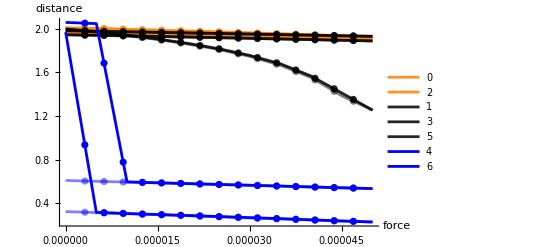

```mathematica
$color=Association["special"->Orange,"orientable"->Blue,"nonorientable"->Black];
Show[
Show[
ListPlot[testdata[[{1,3},1;;11,{"f","d"}]],Joined->True,Mesh->True,PlotLegends->{0,2},AxesLabel->{"force","distance"},
PlotStyle->{{$color["special"],Opacity[0.85]},{$color["special"],Opacity[0.85]}},PlotRange->All
],

ListPlot[testdata[[{1,3},11;;,{"f","d"}]],Joined->True,Mesh->True,AxesLabel->{"force","distance"},
PlotStyle->{{$color["special"],Opacity[0.5]},{$color["special"],Opacity[0.5]}},PlotRange->All
]
],

Show[
ListPlot[testdata[[{2,4,6},1;;11,{"f","d"}]],Joined->True,Mesh->True,PlotLegends->{1,3,5},AxesLabel->{"force","distance"},
PlotStyle->{{$color["nonorientable"],Opacity[0.85]},{$color["nonorientable"],Opacity[0.85]}},PlotRange->All
],

ListPlot[testdata[[{2,4,6},11;;,{"f","d"}]],Joined->True,Mesh->True,AxesLabel->{"force","distance"},
PlotStyle->{{$color["nonorientable"],Opacity[0.5]},{$color["nonorientable"],Opacity[0.5]}},PlotRange->All
]
],

Show[
ListPlot[testdata[[{5,7},1;;11,{"f","d"}]],Joined->True,Mesh->True,PlotLegends->{4,6},AxesLabel->{"force","distance"},
PlotStyle->{$color["orientable"],$color["orientable"]},PlotRange->All
],

ListPlot[testdata[[{5,7},11;;,{"f","d"}]],Joined->True,Mesh->True,AxesLabel->{"force","distance"},
PlotStyle->{{$color["orientable"],Opacity[0.5]},{$color["orientable"],Opacity[0.5]}},PlotRange->All
]
]
,
PlotRange->All,
AxesOrigin->{0,0}
]
```

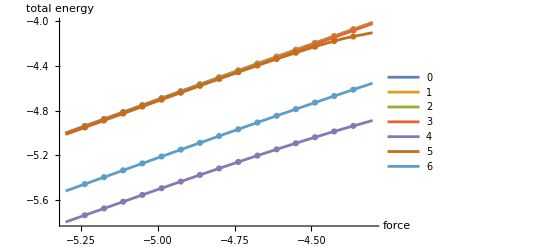

```mathematica
ListPlot[Log[10,#]& /@ lowestEnergy[testdata][[All,All,{3,5}]],PlotRange->All,Joined->True,Mesh->True,PlotLegends->Range[0,6],AxesLabel->{"force","total energy"}]
```

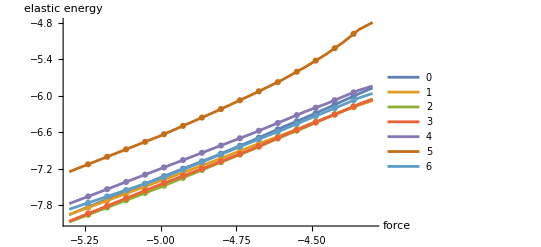

```mathematica
ListPlot[Log[10,#]& /@lowestEnergy[testdata][[All,All,{3,6}]],PlotRange->All,Joined->True,Mesh->True,PlotLegends->Range[0,6],AxesLabel->{"force","elastic energy"}]
```

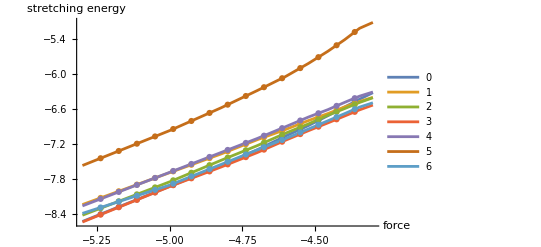

```mathematica
ListPlot[Log[10,#]& /@lowestEnergy[testdata][[All,All,{3,7}]],PlotRange->All,Joined->True,Mesh->True,PlotLegends->Range[0,6], AxesLabel->{"force","stretching energy"}]
```

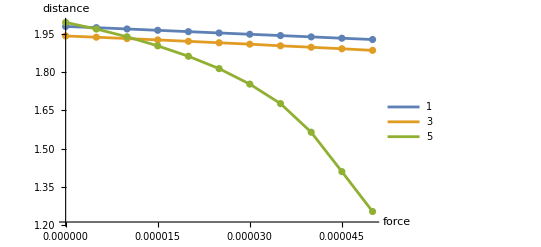

```mathematica
ListPlot[
Table[(({#[[1]], #[[2]]}&)@dist[q,#])&/@Range[mforce[q]],{q,1,qmax,2}],
Joined->True,PlotLegends->Range[1,qmax,2],Mesh->True,PlotRange->All,
AxesLabel->{"force", "distance"}
]
```

### Thicknesses

#### q=0

```mathematica
$fileList={
"simulation results/bending E-3/cycle 6 res=300 step=0p000005 b=0p001 {13528, 9778} v3 q = 0",
"simulation results/bending E-4/cycle 3 res=180 step=0p000005 b=0p0001 {4908, 3558} v3 q = 0",
"simulation results/bending E-5/cycle 3 res=180 step=0p000001 b=0p00001 {4908, 3558} v3 q = 0"
(*,
"simulation results/bending E-6/cycle 6 res=300 step=0p00000005 b=0p000001 {13528, 9778} v3 q = 0",
"simulation results/bending E-7/cycle 3 res=180 step=0p00000004 b=0p0000001 {4908, 3558} v3 q = 0"*)
};
```

```mathematica
data = 
loadData[
Echo[#],

(*test to make sure this is the file we want.*)
True&,

 "Verbose" -> False
]&/@$fileList;
qmax=0;
```

simulation results/bending E-3/cycle 6 res=300 step=0p000005 b=0p001 {13528, 9778} v3 q = 0

simulation results/bending E-4/cycle 3 res=180 step=0p000005 b=0p0001 {4908, 3558} v3 q = 0

simulation results/bending E-5/cycle 3 res=180 step=0p000001 b=0p00001 {4908, 3558} v3 q = 0

```mathematica
testdata=processData[data];
```

53.3819

3.68266

3.69064

```mathematica
maxForceAt=Table[Last[SortBy[{"n","f"}/.testdata[[q,All,{"n","f"}]],Last]][[1]],{q,1,3}]
```

{21,11,11}

```mathematica
{"n","d","f"}/.testdata[[1,1;;maxForceAt[[1]],{"n","d","f"}]]
```

{{1,2.00256,0.},{2,2.00106,5.×10^-6},{3,1.99937,0.00001},{4,1.99716,0.000015},{5,1.99525,0.00002},{6,1.99329,0.000025},{7,1.99137,0.00003},{8,1.98924,0.000035},{9,1.98726,0.00004},{10,1.98489,0.000045},{11,1.98313,0.00005},{12,1.9804,0.000055},{13,1.97795,0.00006},{14,1.97541,0.000065},{15,1.97287,0.00007},{16,1.9702,0.000075},{17,1.96755,0.00008},{18,1.96436,0.000085},{19,1.96127,0.00009},{20,1.95809,0.000095},{21,1.9549,0.0001}}

```mathematica
{"n","d","f"}/.testdata[[2,1;;maxForceAt[[2]],{"n","d","f"}]]
```

{{1,2.00748,0.},{2,2.00037,5.×10^-6},{3,1.99247,0.00001},{4,1.98439,0.000015},{5,1.97624,0.00002},{6,1.96762,0.000025},{7,1.95918,0.00003},{8,1.95034,0.000035},{9,1.93939,0.00004},{10,1.92898,0.000045},{11,1.91865,0.00005}}

```mathematica
{"n","d","f"}/.testdata[[3,1;;maxForceAt[[3]],{"n","d","f"}]]
```

{{1,2.00611,0.},{2,1.99481,1.×10^-6},{3,1.98272,2.×10^-6},{4,1.97223,3.×10^-6},{5,1.95791,4.×10^-6},{6,1.94584,5.×10^-6},{7,1.93177,6.×10^-6},{8,1.91825,7.×10^-6},{9,1.90507,8.×10^-6},{10,1.89103,9.×10^-6},{11,1.87698,0.00001}}

```mathematica
{"n","d","f"}/.testdata[[4,1;;maxForceAt[[4]],{"n","d","f"}]]
```

{{1,2.00178,0.},{2,2.0017,5.×10^-8},{3,2.00164,1.×10^-7},{4,2.00147,1.5×10^-7},{5,2.00142,2.×10^-7},{6,2.0014,2.5×10^-7},{7,1.98886,3.×10^-7},{8,1.98874,3.5×10^-7},{9,1.98869,4.×10^-7},{10,1.98824,4.5×10^-7},{11,1.94893,5.×10^-7},{12,1.94887,5.5×10^-7},{13,1.935,6.×10^-7},{14,1.93494,6.5×10^-7},{15,1.90742,7.×10^-7},{16,1.90735,7.5×10^-7},{17,1.90717,8.×10^-7},{18,1.90708,8.5×10^-7},{19,1.86575,9.×10^-7},{20,1.86571,9.5×10^-7},{21,1.8462,1.×10^-6}}

```mathematica
values={11,8,15};
```

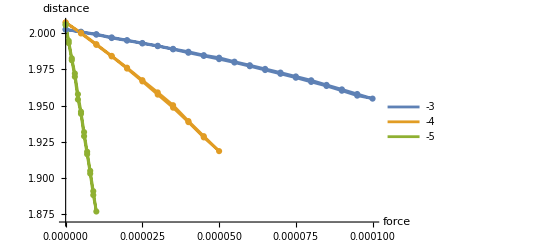

```mathematica
Show[
ListPlot[
testdata[[All,1;;,{"f","d"}]],Joined->True,PlotLegends->{-3,-4,-5,-6,-7},AxesLabel->{"force","distance"},
PlotRange->{{0,0.0001},All}
],
ListPlot[
testdata[[All,1;;,{"f","d"}]],Joined->False,AxesLabel->{"force","distance"},
PlotRange->{{0,0.0001},All}
]
]
```

```mathematica
mcchart=MapThread[
toChartFunction[
data[[#1]],
VertexMeanCurvature[ data[[#1]]["shape"], data[[#1]]["data"][[#2]], Range[MeshCellCount[data[[#1]]["shape"],0]]]
]&,
{{1,2,3,4,5},
values}
];
```

```mathematica
MapThread[
plotSurface[#1["chart"], colorVariables[#2,#3]]&,
{data, mcchart,{0.3,0.3,0.3,0.3,0.3}}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
strain=MapThread[
vertexStrainEnergyDensity[ data[[#1,"shape"]], v, data[[#1,"data",#2]]] & ,
{Range[Length[data]],values}
];
Max/@strain
Min/@strain
```

{4.85086×10^-6,1.84811×10^-7,7.80997×10^-9,2.53808×10^-9}

{1.92395×10^-11,1.94443×10^-13,1.30328×10^-15,6.46742×10^-15}

```mathematica
sdata=MapThread[
toChartFunction[
#1,
#2
]&,{data,strain}];
MapThread[
plotSurface[ #1["chart"], colorMagnitude[#2,#3]]&,
{
data,
sdata,
(Max/@strain)/4
}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### q=1

```mathematica
$fileList={
"simulation results/bending E-4/cycle 3 res=246 step=0p000005 b=0p0001 {9125, 6585} v3 q = 1",
"simulation results/bending E-5/cycle 3 res=180 step=0p000001 b=0p00001 {4908, 3558} v3 q = 1",
"simulation results/bending E-6/cycle 3 res=180 step=0p0000001 b=0p000001 {4908, 3558} v3 q = 1",
"simulation results/bending E-7/cycle 3 res=180 step=0p00000004 b=0p0000001 {4908, 3558} v3 q = 1"
};
```

```mathematica
data = 
loadData[
Echo[#],

(*test to make sure this is the file we want.*)
True&,

 "Verbose" -> False
]&/@$fileList;
qmax=0;
```

simulation results/bending E-4/cycle 3 res=246 step=0p000005 b=0p0001 {9125, 6585} v3 q = 1

simulation results/bending E-5/cycle 3 res=180 step=0p000001 b=0p00001 {4908, 3558} v3 q = 1

simulation results/bending E-6/cycle 3 res=180 step=0p0000001 b=0p000001 {4908, 3558} v3 q = 1

simulation results/bending E-7/cycle 3 res=180 step=0p00000004 b=0p0000001 {4908, 3558} v3 q = 1

```mathematica
testdata=processData[data];
```

15.63

3.40345

3.4767

3.50517

```mathematica
maxForceAt=Table[Last[SortBy[{"n","f"}/.testdata[[q,All,{"n","f"}]],Last]][[1]],{q,1,4}]
```

{11,11,11,11}

```mathematica
{"n","d","f"}/.testdata[[1,1;;maxForceAt[[1]],{"n","d","f"}]]
```

{{1,1.98013,0.},{2,1.97545,5.×10^-6},{3,1.97027,0.00001},{4,1.96504,0.000015},{5,1.95974,0.00002},{6,1.95454,0.000025},{7,1.94944,0.00003},{8,1.94432,0.000035},{9,1.93918,0.00004},{10,1.93391,0.000045},{11,1.92876,0.00005}}

```mathematica
{"n","d","f"}/.testdata[[2,1;;maxForceAt[[2]],{"n","d","f"}]]
```

{{1,2.01818,0.},{2,2.01335,1.×10^-6},{3,2.0066,2.×10^-6},{4,1.99991,3.×10^-6},{5,1.99345,4.×10^-6},{6,1.98654,5.×10^-6},{7,1.97949,6.×10^-6},{8,1.97244,7.×10^-6},{9,1.96459,8.×10^-6},{10,1.95674,9.×10^-6},{11,1.94735,0.00001}}

```mathematica
{"n","d","f"}/.testdata[[3,1;;maxForceAt[[3]],{"n","d","f"}]]
```

{{1,2.01841,0.},{2,2.01834,1.×10^-7},{3,2.01719,2.×10^-7},{4,2.01711,3.×10^-7},{5,2.0055,4.×10^-7},{6,2.00537,5.×10^-7},{7,1.99565,6.×10^-7},{8,1.99554,7.×10^-7},{9,1.98544,8.×10^-7},{10,1.98131,9.×10^-7},{11,1.98125,1.×10^-6}}

```mathematica
{"n","d","f"}/.testdata[[4,1;;maxForceAt[[4]],{"n","d","f"}]]
```

{{1,2.01825,0.},{2,2.01813,4.×10^-8},{3,2.01797,8.×10^-8},{4,2.01664,1.2×10^-7},{5,2.01652,1.6×10^-7},{6,2.00314,2.×10^-7},{7,2.003,2.4×10^-7},{8,1.98925,2.8×10^-7},{9,1.98918,3.2×10^-7},{10,1.98378,3.6×10^-7},{11,1.98369,4.×10^-7}}

```mathematica
values={11,11,11,11};
```

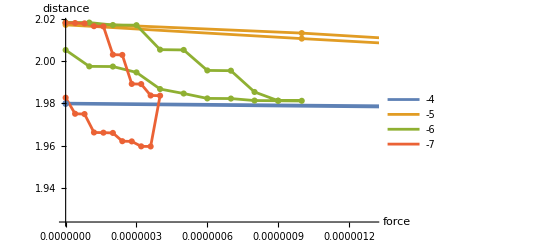

```mathematica
Show[
ListPlot[
testdata[[All,1;;,{"f","d"}]],Joined->True,PlotLegends->{-4,-5,-6,-7},AxesLabel->{"force","distance"},
PlotRange->{{0,0.0000013},All}
],
ListPlot[
testdata[[All,1;;,{"f","d"}]],Joined->False,AxesLabel->{"force","distance"},
PlotRange->{{0,0.0000013},All}
]
]
```

```mathematica
mcchart=MapThread[
toChartFunction[
data[[#1]],
VertexMeanCurvature[ data[[#1]]["shape"], data[[#1]]["data"][[#2]], Range[MeshCellCount[data[[#1]]["shape"],0]]]
]&,
{{1,2,3,4},
values}
];
```

```mathematica
MapThread[
plotSurface[#1["chart"], colorVariables[#2,#3]]&,
{data, mcchart,{0.3,0.3,0.3,0.3}}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
strain=MapThread[
vertexStrainEnergyDensity[ data[[#1,"shape"]], v, data[[#1,"data",#2]]] & ,
{Range[Length[data]],values}
];
Max/@strain
Min/@strain
```

{4.57202×10^-6,5.08265×10^-7,1.42646×10^-8,9.8468×10^-9}

{5.02888×10^-11,9.30717×10^-13,5.30944×10^-15,1.18735×10^-15}

```mathematica
sdata=MapThread[
toChartFunction[
#1,
#2
]&,{data,strain}];
MapThread[
plotSurface[ #1["chart"], colorMagnitude[#2,#3]]&,
{
data,
sdata,
(Max/@strain)/4
}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Decreasing bending rigidity and force strength

Decreasing the bending rigidity and the force strength simultaneously.

#### q=0

```mathematica
data = With[{
$fileList={
"simulation results/test/bending res=210 r=0p5 {6669, 4816} v3 q = 0",
"simulation results/test/bending res=210 r=0p7 {6669, 4816} v3 q = 0",
"simulation results/test/bending res=210 r=1p {6669, 4816} v3 q = 0"
},

q=0
},

qmax=q;

loadData[
Echo[#],

(*all files are good.*)
True&,

 "Verbose" -> False
]&/@$fileList
];
```

simulation results/test/bending res=210 r=0p5 {6669, 4816} v3 q = 0

simulation results/test/bending res=210 r=0p7 {6669, 4816} v3 q = 0

simulation results/test/bending res=210 r=1p {6669, 4816} v3 q = 0

distance vs bending rigidity at fixed force/rigidity

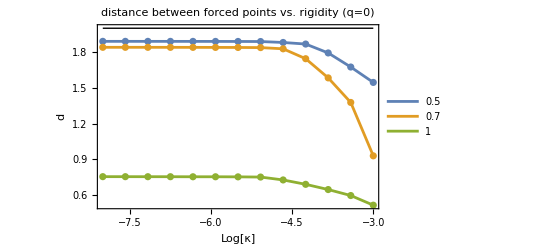

```mathematica
(*Make plot of distance between points and bending rigidity*)
(*legend refers to ratio between force/bending rigidity*)
Show[
ListPlot[
Transpose[{
Log[10,#[["bending rigidity"]]],
distanceMeasureFunction[ #, All][[All,2]]
}]&/@data,

Joined->True,Mesh->True,PlotRange->All,
PlotLegends->{0.5,0.7,1}
],

(*original value*)
Graphics[Line[{{-8,2},{-3,2}}]],

PlotRange->All,
FrameLabel->{"Log[κ]","d"},
Frame->True,
PlotLabel->"distance between forced points vs. rigidity (q=0)"
]
```

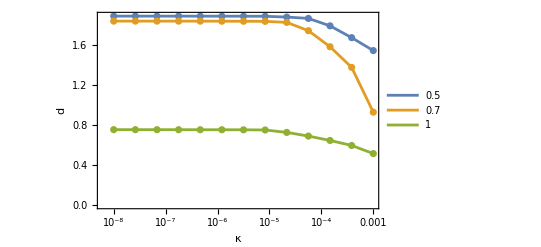

```mathematica
ListLogLinearPlot[Transpose[{
#[["bending rigidity"]],
distanceMeasureFunction[ #, All][[All,2]]
}]&/@data,Joined->True,Mesh->True,PlotRange->All,
PlotLegends->{0.5,0.7,1},FrameLabel->{"κ","d"},Frame->True]
```

At fixed ratio κ/f, as κ decreases the distance between the two points being pulled together reach a plateau. This plateau indicates that as κ goes to zero, the deformation is becoming isometric and that the shape is determined by the energetic balance between bending and force.

```mathematica
data[[1]]//Keys
```

{version,q,chart,shape,map,interacting vertices,bending rigidity,force strength,data}

```mathematica
data[[1,"force strength"]]
```

{0.0005,0.000191559,0.00007339,0.0000281171,0.0000107722,4.12702×10^-6,1.58114×10^-6,6.05764×10^-7,2.32079×10^-7,8.8914×10^-8,3.40646×10^-8,1.30508×10^-8,5.×10^-9}

```mathematica
test= meanCurvatureData[data[[1]],10];

Show[
plotSurface[
DeformMesh[data[[2,"shape"]], data[[2,"data",10]]],
colorVariables[toSurfaceFunction[ data[[2]],test],0.25]
],
Graphics3D[{
Thickness[0.01],
Line[
{
data[[2,"data",10,data[[1,"interacting vertices",1]]]],data[[2,"data",10,data[[1,"interacting vertices",2]]]]
}]}],
Boxed->False
]
```

-Graphics3D-

energy

We can verify this by looking at the balance of stretching to bending to force energies.

```mathematica
energies=MapThread[
{
#1 /. {bendingRigidity->0,f0->0} (*stretching*),
bendingRigidity D[#1,bendingRigidity] (*bending*),
f0 D[#1,f0] (*force*)
} /. {f0->#2, bendingRigidity ->#3}&
,
{
computeEnergy[data[[1]]]/.positionRules[data[[1]]],
data[[1,"force strength"]],
data[[1,"bending rigidity"]]
}
]
```

{{0.0000403558,0.0000922859,0.000772478},{0.0000114659,0.0000269721,0.000320724},{2.70583×10^-6,6.88192×10^-6,0.000131552},{2.1893×10^-7,1.80804×10^-6,0.0000525003},{4.64797×10^-8,6.44806×10^-7,0.0000202571},{1.08734×10^-8,2.33818×10^-7,7.79343×10^-6},{3.11173×10^-9,9.31434×10^-8,2.98676×10^-6},{9.76172×10^-10,3.67413×10^-8,1.14447×10^-6},{2.95837×10^-10,1.44109×10^-8,4.38522×10^-7},{1.26573×10^-10,5.60512×10^-9,1.6802×10^-7},{6.98921×10^-11,2.17855×10^-9,6.43746×10^-8},{1.73644×10^-11,8.45696×10^-10,2.46645×10^-8},{1.73606×10^-11,3.24003×10^-10,9.44942×10^-9}}

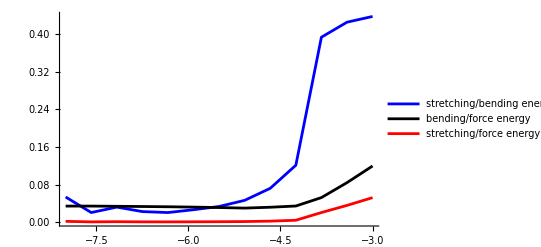

```mathematica
Show[
ListPlot[ Transpose[{Log[10,data[[1,"bending rigidity"]]],energies[[All,1]]/energies[[All,2]]}],Joined->True,PlotStyle->Blue,PlotRange->All,PlotLegends->{"stretching/bending energy"}],
ListPlot[ Transpose[{Log[10,data[[1,"bending rigidity"]]],energies[[All,2]]/energies[[All,3]]}],Joined->True,PlotRange->All,PlotStyle->Black,PlotLegends->{"bending/force energy"}],
ListPlot[ Transpose[{Log[10,data[[1,"bending rigidity"]]],energies[[All,1]]/energies[[All,3]]}],Joined->True,PlotRange->All,PlotStyle->Red,PlotLegends->{"stretching/force energy"}],
PlotRange->All
]
```

For “thinner” membranes, the stretching energy is much smaller than the bending energy, suggesting that the shape is isometric. However, notice that the bending energy is at the same ratio, so that we have

	Estretching << Ebending << Eforce

It makes sense to consider the shape as being determined by the balance of the second two energies.

The mean curvature and strain distribution

```mathematica
Max[Abs[#]]& /@ meanCurvatureData[data[[1]],{1,4,7,10,13}]
meanCurvaturePlot[data[[1]], {1,4,7,10,13}, 1]
```

{2.68684,2.93714,2.06877,1.32242,1.37557}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

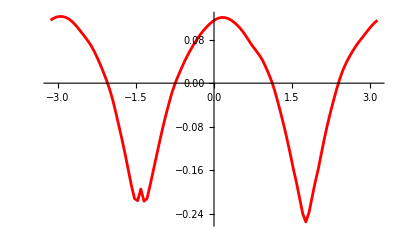

```mathematica
mcdata=meanCurvatureData[data[[1]],10];
g0p5=ListPlot[Select[MapThread[ Flatten[{#1,#2}]&,{MeshCoordinates[data[[1,"chart"]]],mcdata}],Abs[#[[2]]]<0.0001&][[All,{1,3}]],Joined->True,PlotStyle->{Red}]
```

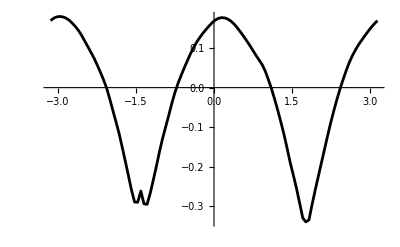

```mathematica
mcdata=meanCurvatureData[data[[2]],10];
g0p7=ListPlot[Select[MapThread[ Flatten[{#1,#2}]&,{MeshCoordinates[data[[1,"chart"]]],mcdata}],Abs[#[[2]]]<0.0001&][[All,{1,3}]],Joined->True,PlotStyle->{Black}]
```

```mathematica
Max/@strainData[data[[1]],{1,4,7,10,13}]
strainPlot[data[[1]],{1,4,7,10,13},10^(-4)]
```

{0.000121586,2.02852×10^-6,4.15472×10^-8,5.60718×10^-9,4.71976×10^-10}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Mean strain

```mathematica
ListPlot[
MapThread[
Log[10,Transpose[{
#1[["bending rigidity"]],
Mean/@#2
}]]&,
{
data,
strainData/@data
}
],
PlotRange->All,Joined->True,Mesh->True,
PlotLegends->{0.5,0.7,1.},
PlotLabel->"Mean strain vs. bending rigidity for fixed force/rigidity",
FrameLabel->{"Log[κ]","Log[γ]"},
Frame->True
]
```

-Graphics-

```mathematica
ListLogLogPlot[
MapThread[
Transpose[{
#1[["bending rigidity"]],
Mean/@#2
}]&,
{
data,
strainData/@data
}
],
PlotRange->All,Joined->True,Mesh->True,
PlotLegends->{0.5,0.7,1.},
PlotLabel->"Mean strain vs. bending rigidity for fixed force/rigidity",
FrameLabel->{"κ","average γ"},
Frame->True
]
```

-Graphics-

#### q=1

```mathematica
data = With[{
$fileList={
"simulation results/test/bending res=210 r=0p5 {6669, 4816} v3 q = 1",
"simulation results/test/bending res=210 r=0p7 {6669, 4816} v3 q = 1",
"simulation results/test/bending res=210 r=1p {6669, 4816} v3 q = 1"
},
q=1
},

qmax=q;

loadData[
Echo[#],

(*test to make sure this is the file we want.*)
True&,

 "Verbose" -> False
]&/@$fileList
];
```

simulation results/test/bending res=210 r=0p5 {6669, 4816} v3 q = 1

simulation results/test/bending res=210 r=0p7 {6669, 4816} v3 q = 1

simulation results/test/bending res=210 r=1p {6669, 4816} v3 q = 1

distance vs bending rigidity at fixed force/rigidity

```mathematica
(*Make plot of distance between points and bending rigidity*)
(*legend refers to ratio between force/bending rigidity*)
Show[
ListPlot[
Transpose[{
Log[10,#[["bending rigidity"]]],
distanceMeasureFunction[ #, All][[All,2]]
}]&/@data,
Joined->True,Mesh->True,PlotRange->All,
PlotLegends->{0.5,0.7,1}
],
Graphics[Line[{{-8,2},{-3,2}}]],
PlotRange->All,AxesOrigin->{-8,0}
]
```

-Graphics-

```mathematica
ListLogLinearPlot[Transpose[{
#[["bending rigidity"]],
distanceMeasureFunction[ #, All][[All,2]]
}]&/@data,Joined->True,Mesh->True,PlotRange->All,
PlotLegends->{0.5,0.7,1},FrameLabel->{"κ","d"},Frame->True]
```

-Graphics-

```mathematica
test= meanCurvatureData[data[[1]],10];

Show[
plotSurface[
DeformMesh[data[[2,"shape"]], data[[2,"data",10]]],
colorVariables[toSurfaceFunction[ data[[2]],test],0.25]
],
Graphics3D[{
Thickness[0.01],
Line[
{
data[[2,"data",10,data[[1,"interacting vertices",1]]]],data[[2,"data",10,data[[1,"interacting vertices",2]]]]
}]}],
Boxed->False
]
```

-Graphics3D-

energy

```mathematica
energies=MapThread[
{
#1 /. {bendingRigidity->0,f0->0},
bendingRigidity D[#1,bendingRigidity],
f0 D[#1,f0]
} /. {f0->#2, bendingRigidity ->#3}&
,
{
computeEnergy[data[[#]]]/.positionRules[data[[#]]],
data[[#,"force strength"]],
data[[#,"bending rigidity"]]
}
]&@2
```

{{0.000044544,0.000083194,0.00113793},{0.0000122154,0.0000251808,0.000461211},{3.88748×10^-6,9.28612×10^-6,0.000181958},{3.79762×10^-7,2.16476×10^-6,0.0000727557},{1.02023×10^-7,7.87172×10^-7,0.0000280744},{3.04125×10^-8,2.93274×10^-7,0.0000108047},{1.06321×10^-8,1.19739×10^-7,4.14373×10^-6},{3.99759×10^-9,4.96143×10^-8,1.58773×10^-6},{1.44588×10^-9,2.03603×10^-8,6.0842×10^-7},{6.10031×10^-10,8.28833×10^-9,2.33109×10^-7},{2.62156×10^-10,3.37461×10^-9,8.93112×10^-8},{1.01346×10^-10,1.38468×10^-9,3.42179×10^-8},{8.36503×10^-11,5.40394×10^-10,1.31098×10^-8}}

```mathematica
Show[
ListPlot[ Transpose[{Log[10,data[[2,"bending rigidity"]]],energies[[All,1]]/energies[[All,2]]}],Joined->True,PlotStyle->Blue,PlotRange->All,PlotLegends->{"stretching/bending energy"}],
ListPlot[ Transpose[{Log[10,data[[2,"bending rigidity"]]],energies[[All,2]]/energies[[All,3]]}],Joined->True,PlotRange->All,PlotStyle->Black,PlotLegends->{"bending/force energy"}],
ListPlot[ Transpose[{Log[10,data[[2,"bending rigidity"]]],energies[[All,1]]/energies[[All,3]]}],Joined->True,PlotRange->All,PlotStyle->Red,PlotLegends->{"stretching/force energy"}],
PlotRange->All
]
```

-Graphics-

What is interesting here is that smaller thicknesses are necessary to suppress the strain and the strain energy is still about 15% of the bending energy.

The mean curvature distribution

```mathematica
meanCurvaturePlot[data[[3]], {1,6,10}, 1]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
bendingEnergyDensity=data[[3,"bending rigidity",6]] meanCurvatureData[ data[[3]], 6 ]^2;
strainEnergyDensity=strainData[data[[1]],6];
```

```mathematica
(*All the places the stretching energy is comparable to the bending energy *)
plotSurface[data[[3,"chart"]], colorMagnitude[If[#<1,0,1]&/@(strainEnergyDensity/bendingEnergyDensity), 0.5]]
```

-Graphics-

```mathematica
(*stretching energy greater than 10% to bending energy*)
plotSurface[data[[3,"chart"]], colorMagnitude[If[#<0.1,0,1]&/@(strainEnergyDensity/bendingEnergyDensity), 0.5]]
```

-Graphics-

Strain maps

```mathematica
strainFunction[d_]:=vertexStrainEnergyDensity[ d[["shape"]], v, #]&/@d[["data"]]
strainMap=strainFunction[#]&/@data;
```

```mathematica
ListPlot[
MapThread[
Log[10,Transpose[{
#1[["bending rigidity"]],
Mean/@#2
}]]&,
{
data,
strainMap
}
],
PlotRange->All,Joined->True,Mesh->True,
PlotLegends->{0.5,0.7},
PlotLabel->"Mean strain vs. bending rigidity for fixed force/rigidity"
]
```

-Graphics-

```mathematica
ListLogLogPlot[
MapThread[
Transpose[{
#1[["bending rigidity"]],
Mean/@#2
}]&,
{
data,
strainData/@data
}
],
PlotRange->All,Joined->True,Mesh->True,
PlotLegends->{0.5,0.7,1.},
PlotLabel->"Mean strain vs. bending rigidity for fixed force/rigidity",
FrameLabel->{"κ","average γ"},
Frame->True
]
```

-Graphics-

```mathematica
strain=N@Map[vertexStrainEnergyDensity[ data[[1,"shape"]], v, data[[1,"data",#]]] &,
{1,6,10}
];
```

```mathematica
sdata=Map[
toChartFunction[
data[[1]],
#
]&,strain];
MapThread[
Show[plotSurface[ data[[1,"chart"]], colorMagnitude[#1,#2]],PlotLabel->#3]&,
{
sdata,
(Max/@strain)/4,
data[[1,"bending rigidity"]][[{1,6,10}]]
}
]
```

{-Graphics-,-Graphics-,-Graphics-}

#### q=2

```mathematica
$fileList={
"simulation results/test/bending res=210 r=0p5 {6669, 4816} v3 q = 2",
"simulation results/test/bending res=210 r=0p7 {6669, 4816} v3 q = 2",
"simulation results/test/bending res=210 r=0p9 {6669, 4816} v3 q = 2",
"simulation results/test/bending res=210 r=1p {6669, 4816} v3 q = 2"
};
```

```mathematica
data = 
loadData[
Echo[#],

(*test to make sure this is the file we want.*)
True&,

 "Verbose" -> False
]&/@$fileList;
qmax=2;
```

simulation results/test/bending res=210 r=0p5 {6669, 4816} v3 q = 2

simulation results/test/bending res=210 r=0p7 {6669, 4816} v3 q = 2

simulation results/test/bending res=210 r=0p9 {6669, 4816} v3 q = 2

simulation results/test/bending res=210 r=1p {6669, 4816} v3 q = 2

distance vs bending rigidity at fixed force/rigidity

```mathematica
(*Make plot of distance between points and bending rigidity*)
(*legend refers to ratio between force/bending rigidity*)
Show[
ListPlot[
Transpose[{
Log[10,#[["bending rigidity"]]],
distanceMeasureFunction[ #, All][[All,2]]
}]&/@data,

Joined->True,Mesh->True,PlotRange->All,
PlotLegends->{0.5,0.7,0.9,1}
],

(*original value*)
Graphics[Line[{{-7,2},{-3,2}}]],

PlotRange->All,
FrameLabel->{"Log[κ]","d"},
Frame->True,
PlotLabel->"distance between forced points vs. rigidity (q=2)"
]
```

-Graphics-

The mean curvature distribution

```mathematica
data[[1,"force strength"]]/data[[1,"bending rigidity"]]
mcchart=Map[
toChartFunction[
data[[1]],
VertexMeanCurvature[ data[[1]]["shape"], data[[1,"data",#]], Range[MeshCellCount[data[[1]]["shape"],0]]]
]&,
{1,3,5,7}
];
MapThread[
Show[plotSurface[data[[1,"chart"]], colorVariables[#1,#2]],PlotLabel->#3]&,
{ mcchart,{0.5,0.5,0.5,0.5},data[[1,"bending rigidity",{1,3,5,7}]]}
]
```

{0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Strain maps

```mathematica
strainFunction[d_]:=vertexStrainEnergyDensity[ d[["shape"]], v, #]&/@d[["data"]]
strainMap=strainFunction[#]&/@data;
```

```mathematica
ListPlot[
MapThread[
Log[10,Transpose[{
#1[["bending rigidity"]],
Mean/@#2
}]]&,
{
data,
strainMap
}
],
PlotRange->All,Joined->True,Mesh->True,
PlotLegends->{0.5,0.7},
PlotLabel->"Mean strain vs. bending rigidity for fixed force/rigidity"
]
```

-Graphics-

```mathematica
strain=N@Map[vertexStrainEnergyDensity[ data[[1,"shape"]], v, data[[1,"data",#]]] &,
{1,2,3,4}
];
```

```mathematica
sdata=Map[
toChartFunction[
data[[1]],
#
]&,strain];
MapThread[
Show[plotSurface[ data[[1,"chart"]], colorMagnitude[#1,#2]],PlotLabel->#3]&,
{
sdata,
(Max/@strain)/4,
data[[1,"bending rigidity"]][[{1,2,3,4}]]
}
]
```

#### q=3

```mathematica
$fileList={
"simulation results/test/bending res=210 r=0p5 {6669, 4816} v3 q = 3",
"simulation results/test/bending res=210 r=0p7 {6669, 4816} v3 q = 3",
"simulation results/test/bending res=210 r=1p {6669, 4816} v3 q = 3"
};
```

```mathematica
data = 
loadData[
Echo[#],

(*test to make sure this is the file we want.*)
True&,

 "Verbose" -> False
]&/@$fileList;
qmax=2;
```

simulation results/test/bending res=210 r=0p5 {6669, 4816} v3 q = 3

simulation results/test/bending res=210 r=0p7 {6669, 4816} v3 q = 3

simulation results/test/bending res=210 r=1p {6669, 4816} v3 q = 3

distance vs bending rigidity at fixed force/rigidity

```mathematica
(*Make plot of distance between points and bending rigidity*)
(*legend refers to ratio between force/bending rigidity*)
Show[
ListPlot[
Transpose[{
Log[10,#[["bending rigidity"]]],
distanceMeasureFunction[ #, All][[All,2]]
}]&/@data,

Joined->True,Mesh->True,PlotRange->All,
PlotLegends->{0.5,0.7,0.9,1}
],

(*original value*)
Graphics[Line[{{-7,2},{-3,2}}]],

PlotRange->All,
FrameLabel->{"Log[κ]","d"},
Frame->True,
PlotLabel->"distance between forced points vs. rigidity (q=3)"
]
```

-Graphics-

The mean curvature distribution

```mathematica
data[[1,"force strength"]]/data[[1,"bending rigidity"]]
mcchart=Map[
toChartFunction[
data[[1]],
VertexMeanCurvature[ data[[1]]["shape"], data[[1,"data",#]], Range[MeshCellCount[data[[1]]["shape"],0]]]
]&,
{1,3,5,7}
];
MapThread[
Show[plotSurface[data[[1,"chart"]], colorVariables[#1,#2]],PlotLabel->#3]&,
{ mcchart,{0.5,0.5,0.5,0.5},data[[1,"bending rigidity",{1,3,5,7}]]}
]
```

{0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Strain maps

```mathematica
strainFunction[d_]:=vertexStrainEnergyDensity[ d[["shape"]], v, #]&/@d[["data"]]
strainMap=strainFunction[#]&/@data;
```

```mathematica
ListPlot[
MapThread[
Log[10,Transpose[{
#1[["bending rigidity"]],
Mean/@#2
}]]&,
{
data,
strainMap
}
],
PlotRange->All,Joined->True,Mesh->True,
PlotLegends->{0.5,0.7,1},
PlotLabel->"Mean strain vs. bending rigidity for fixed force/rigidity"
]
```

-Graphics-

```mathematica
strain=N@Map[vertexStrainEnergyDensity[ data[[1,"shape"]], v, data[[1,"data",#]]] &,
{1,2,3,4}
];
```

```mathematica
sdata=Map[
toChartFunction[
data[[1]],
#
]&,strain];
MapThread[
Show[plotSurface[ data[[1,"chart"]], colorMagnitude[#1,#2]],PlotLabel->#3]&,
{
sdata,
(Max/@strain)/4,
data[[1,"bending rigidity"]][[{1,2,3,4}]]
}
]
```

#### q=4

```mathematica
$fileList={
"simulation results/test/bending res=210 r=0p5 {6669, 4816} v3 q = 4"
};
```

```mathematica
data = 
loadData[
Echo[#],

(*test to make sure this is the file we want.*)
True&,

 "Verbose" -> False
]&/@$fileList;
qmax=4;
```

simulation results/test/bending res=210 r=0p5 {6669, 4816} v3 q = 4

distance vs bending rigidity at fixed force/rigidity

```mathematica
(*Make plot of distance between points and bending rigidity*)
(*legend refers to ratio between force/bending rigidity*)
Show[
ListPlot[
Transpose[{
Log[10,#[["bending rigidity"]]],
distanceMeasureFunction[ #, All][[All,2]]
}]&/@data,
Joined->True,Mesh->True,PlotRange->All,
PlotLegends->{0.5,0.7,1}
],
PlotRange->All
]
```

-Graphics-

The mean curvature distribution

```mathematica
data[[1,"force strength"]]/data[[1,"bending rigidity"]]
mcchart=Map[
toChartFunction[
data[[1]],
VertexMeanCurvature[ data[[1]]["shape"], data[[1,"data",#]], Range[MeshCellCount[data[[1]]["shape"],0]]]
]&,
{1,3,5,7}
];
MapThread[
Show[plotSurface[data[[1,"chart"]], colorVariables[#1,#2]],PlotLabel->#3]&,
{ mcchart,{0.5,0.5,0.5,0.5},data[[1,"bending rigidity",{1,3,5,7}]]}
]
```

{0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Strain maps

```mathematica
strainFunction[d_]:=vertexStrainEnergyDensity[ d[["shape"]], v, #]&/@d[["data"]]
strainMap=strainFunction[#]&/@data;
```

```mathematica
ListPlot[
MapThread[
Log[10,Transpose[{
#1[["bending rigidity"]],
Mean/@#2
}]]&,
{
data,
strainMap
}
],
PlotRange->All,Joined->True,Mesh->True,
PlotLegends->{0.5,0.7},
PlotLabel->"Mean strain vs. bending rigidity for fixed force/rigidity"
]
```

-Graphics-

```mathematica
strain=N@Map[vertexStrainEnergyDensity[ data[[1,"shape"]], v, data[[1,"data",#]]] &,
{1,2,3,4}
];
```

```mathematica
sdata=Map[
toChartFunction[
data[[1]],
#
]&,strain];
MapThread[
Show[plotSurface[ data[[1,"chart"]], colorMagnitude[#1,#2]],PlotLabel->#3]&,
{
sdata,
(Max/@strain)/4,
data[[1,"bending rigidity"]][[{1,2,3,4}]]
}
]
```

### Increasing thickness directly

#### q=0

```mathematica
data = With[{
$fileList={
"simulation results/test/bending res=210 f=0p00005 {6669, 4816} v3 q = 0"
},
q=0},

qmax=q;

loadData[
Echo[#],

(*test to make sure this is the file we want.*)
True&,

 "Verbose" -> False
]&/@$fileList
];
```

simulation results/test/bending res=210 f=0p00005 {6669, 4816} v3 q = 0

distance vs bending rigidity at fixed force/rigidity

```mathematica
(*Make plot of distance between points and bending rigidity*)
(*legend refers to ratio between force/bending rigidity*)
Show[
ListPlot[
Transpose[{
Log[10,#[["bending rigidity"]]],
distanceMeasureFunction[ #, All][[All,2]]
}]&/@data,
Joined->True,Mesh->True,PlotRange->All,
PlotLegends->{5*10^(-4)}
],
Graphics[Line[{{-8,2},{-3,2}}]],
PlotRange->All,
FrameLabel->{"Log[κ]","d"},
Frame->True,
PlotLabel->"distance between forced points vs. rigidity"
]
```

-Graphics-

energy

```mathematica
energies=MapThread[
{
#1 /. {bendingRigidity->0,f0->0},
bendingRigidity D[#1,bendingRigidity],
f0 D[#1,f0]} /. {f0->#2, bendingRigidity ->#3}&
,
{
computeEnergy[data[[1]]]/.positionRules[data[[1]]],
data[[1,"force strength"]],
data[[1,"bending rigidity"]]
}
]
```

{{8.18183×10^-7,3.54984×10^-6,0.0000923035},{2.93437×10^-7,8.4756×10^-7,0.0000980822},{1.97628×10^-7,2.33762×10^-7,0.0000994399},{1.36997×10^-7,8.29047×10^-8,0.0000998436},{9.41666×10^-8,3.77239×10^-8,0.000100008},{8.0695×10^-8,1.41674×10^-8,0.000100078}}

```mathematica
Show[
ListPlot[ Transpose[{data[[1,"bending rigidity"]],energies[[All,1]]}],Joined->True,PlotStyle->Blue,PlotRange->All,PlotLegends->{"stretching energy"}],
ListPlot[ Transpose[{data[[1,"bending rigidity"]],energies[[All,2]]}],Joined->True,PlotRange->All,PlotStyle->Black,PlotLegends->{"bending energy"}],

PlotRange->All
]
```

-Graphics-

```mathematica
Show[
ListPlot[ Transpose[{Log[10,data[[1,"bending rigidity"]]],energies[[All,1]]/energies[[All,2]]}],Joined->True,PlotStyle->Blue,PlotRange->All,PlotLegends->{"stretching/bending energy"}],

PlotRange->All
]
```

-Graphics-

```mathematica
Show[
ListPlot[ Transpose[{Log[10,data[[1,"bending rigidity"]]],Log[10,energies[[All,1]]/energies[[All,2]]]}],Joined->True,PlotStyle->Blue,PlotRange->All,PlotLegends->{"stretching/bending energy"}],

PlotRange->All
]
```

-Graphics-

```mathematica
Show[
ListPlot[ energies[[All,1]]/energies[[All,2]],Joined->True,PlotStyle->Blue,PlotRange->All,PlotLegends->{"stretching/bending energy"}],
ListPlot[ energies[[All,2]]/energies[[All,3]],Joined->True,PlotRange->All,PlotStyle->Black,PlotLegends->{"bending/force energy"}],
ListPlot[ energies[[All,1]]/energies[[All,3]],Joined->True,PlotRange->All,PlotStyle->Red,PlotLegends->{"stretching/force energy"}],
PlotRange->All
]
```

-Graphics-

```mathematica
Show[
ListPlot[ energies[[All,2]]/energies[[All,3]],Joined->True,PlotRange->All,PlotStyle->Black,PlotLegends->{"bending/force energy"}],
ListPlot[ energies[[All,1]]/energies[[All,3]],Joined->True,PlotRange->All,PlotStyle->Red,PlotLegends->{"stretching/force energy"}],
PlotRange->All
]
```

-Graphics-

The mean curvature distribution

```mathematica
data[[1,"force strength"]]/data[[1,"bending rigidity"]]
mcchart=Map[
toChartFunction[
data[[1]],
VertexMeanCurvature[ data[[1]]["shape"], data[[1,"data",#]], Range[MeshCellCount[data[[1]]["shape"],0]]]
]&,
{1,3,5}
];
MapThread[
Show[plotSurface[data[[1,"chart"]], colorVariables[#1,#2]],PlotLabel->#3]&,
{ mcchart,{0.5,0.5,0.5},data[[1,"bending rigidity",{1,3,5}]]}
]
```

{0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5}

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
data[[2,"force strength"]]/data[[2,"bending rigidity"]]
mcchart=Map[
toChartFunction[
data[[2]],
VertexMeanCurvature[ data[[2]]["shape"], data[[2,"data",#]], Range[MeshCellCount[data[[2]]["shape"],0]]]
]&,
{1,3,5}
];
MapThread[
Show[plotSurface[data[[2,"chart"]], colorVariables[#1,#2]],PlotLabel->#3]&,
{ mcchart,{0.25,0.25,0.25},data[[2,"bending rigidity",{1,3,5}]]}
]
```

{0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7}

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
data[[3,"force strength"]]/data[[3,"bending rigidity"]]
mcchart=Map[
toChartFunction[
data[[3]],
VertexMeanCurvature[ data[[3]]["shape"], data[[3,"data",#]], Range[MeshCellCount[data[[3]]["shape"],0]]]
]&,
{1,3,5}
];
MapThread[
Show[plotSurface[data[[3,"chart"]], colorVariables[#1,#2]],PlotLabel->#3]&,
{ mcchart,{0.25,0.25,0.25},data[[3,"bending rigidity",{1,3,5}]]}
]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{-Graphics-,-Graphics-,-Graphics-}

Strain maps

```mathematica
strainFunction[d_]:=vertexStrainEnergyDensity[ d[["shape"]], v, #]&/@d[["data"]]
strainMap=strainFunction[#]&/@data;
```

```mathematica
ListPlot[
MapThread[
Log[10,Transpose[{
#1[["bending rigidity"]],
Mean/@#2
}]]&,
{
data,
strainMap
}
],
PlotRange->All,Joined->True,Mesh->True,
PlotLegends->{0.5,0.7,1.},
PlotLabel->"Mean strain vs. bending rigidity for fixed force/rigidity",
FrameLabel->{"Log[κ]","Log[γ]"},
Frame->True
]
```

-Graphics-

```mathematica
sdata=MapThread[
toChartFunction[
data[[1]],
#
]&,strainMap];
MapThread[
plotSurface[ data[[1,"chart"]], colorMagnitude[#1,#2]]&,
{
sdata,
(Max/@strainMap)/4
}
]
```

$Aborted

MapThread::mptd: Object sdata at position {2, 1} in MapThread[plotSurface[data⟦1,chart⟧,colorMagnitude[#1,#2]]&,{sdata,{1.66555×10^-6,1.15258×10^-6,7.32331×10^-7,3.98782×10^-7,1.28191×10^-7,1.14151×10^-10}}] has only 0 of required 1 dimensions.

MapThread[plotSurface[data⟦1,chart⟧,colorMagnitude[#1,#2]]&,{sdata,{1.66555×10^-6,1.15258×10^-6,7.32331×10^-7,3.98782×10^-7,1.28191×10^-7,1.14151×10^-10}}]

#### q=1

```mathematica
data = With[{
$fileList={
"simulation results/test/bending res=210 f=0p00005 {6669, 4816} v3 q = 1"
},
q=1},

qmax=q;

loadData[
Echo[#],

(*test to make sure this is the file we want.*)
True&,

 "Verbose" -> False
]&/@$fileList
];
```

simulation results/test/bending res=210 f=0p00005 {6669, 4816} v3 q = 1

distance vs bending rigidity at fixed force/rigidity

```mathematica
(*Make plot of distance between points and bending rigidity*)
(*legend refers to ratio between force/bending rigidity*)
Show[
ListPlot[
Transpose[{
Log[10,#[["bending rigidity"]]],
distanceMeasureFunction[ #, All][[All,2]]
}]&/@data,
Joined->True,Mesh->True,PlotRange->All,
PlotLegends->{5*10^(-4)}
],
Graphics[Line[{{-8,2},{-3,2}}]],
PlotRange->All
]
```

-Graphics-

energy

```mathematica
energies=MapThread[
{
#1 /. {bendingRigidity->0,f0->0},
bendingRigidity D[#1,bendingRigidity],
f0 D[#1,f0]} /. {f0->#2, bendingRigidity ->#3}&
,
{
computeEnergy[data[[1]]]/.positionRules[data[[1]]],
data[[1,"force strength"]],
data[[1,"bending rigidity"]]
}
]
```

{{4.73936×10^-7,1.84864×10^-6,0.0000939744},{3.61736×10^-7,4.64103×10^-7,0.0000968208},{3.03197×10^-7,1.60607×10^-7,0.0000975618},{2.32706×10^-7,8.62891×10^-8,0.0000978633},{1.80076×10^-7,4.99913×10^-8,0.0000980434},{1.64421×10^-7,2.08722×10^-8,0.0000981343}}

```mathematica
Show[
ListPlot[ Transpose[{data[[1,"bending rigidity"]],energies[[All,1]]}],Joined->True,PlotStyle->Blue,PlotRange->All,PlotLegends->{"stretching energy"}],
ListPlot[ Transpose[{data[[1,"bending rigidity"]],energies[[All,2]]}],Joined->True,PlotRange->All,PlotStyle->Black,PlotLegends->{"bending energy"}],

PlotRange->All
]
```

-Graphics-

```mathematica
Show[
ListPlot[ Transpose[{Log[10,data[[1,"bending rigidity"]]],energies[[All,1]]/energies[[All,2]]}],Joined->True,PlotStyle->Blue,PlotRange->All,PlotLegends->{"stretching/bending energy"}],

PlotRange->All
]
```

-Graphics-

```mathematica
Show[
ListPlot[ energies[[All,1]]/energies[[All,2]],Joined->True,PlotStyle->Blue,PlotRange->All,PlotLegends->{"stretching/bending energy"}],
ListPlot[ energies[[All,2]]/energies[[All,3]],Joined->True,PlotRange->All,PlotStyle->Black,PlotLegends->{"bending/force energy"}],
ListPlot[ energies[[All,1]]/energies[[All,3]],Joined->True,PlotRange->All,PlotStyle->Red,PlotLegends->{"stretching/force energy"}],
PlotRange->All
]
```

-Graphics-

```mathematica
Show[
ListPlot[ energies[[All,2]]/energies[[All,3]],Joined->True,PlotRange->All,PlotStyle->Black,PlotLegends->{"bending/force energy"}],
ListPlot[ energies[[All,1]]/energies[[All,3]],Joined->True,PlotRange->All,PlotStyle->Red,PlotLegends->{"stretching/force energy"}],
PlotRange->All
]
```

-Graphics-

The mean curvature distribution

```mathematica
data[[1,"force strength"]]/data[[1,"bending rigidity"]]
mcchart=Map[
toChartFunction[
data[[1]],
VertexMeanCurvature[ data[[1]]["shape"], data[[1,"data",#]], Range[MeshCellCount[data[[1]]["shape"],0]]]
]&,
{1,3,5}
];
MapThread[
Show[plotSurface[data[[1,"chart"]], colorVariables[#1,#2]],PlotLabel->#3]&,
{ mcchart,{0.5,0.5,0.5},data[[1,"bending rigidity",{1,3,5}]]}
]
```

{0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5}

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
data[[2,"force strength"]]/data[[2,"bending rigidity"]]
mcchart=Map[
toChartFunction[
data[[2]],
VertexMeanCurvature[ data[[2]]["shape"], data[[2,"data",#]], Range[MeshCellCount[data[[2]]["shape"],0]]]
]&,
{1,3,5}
];
MapThread[
Show[plotSurface[data[[2,"chart"]], colorVariables[#1,#2]],PlotLabel->#3]&,
{ mcchart,{0.5,0.5,0.5},data[[2,"bending rigidity",{1,3,5}]]}
]
```

{0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7}

{-Graphics-,-Graphics-,-Graphics-}

Strain maps

```mathematica
strainFunction[d_]:=vertexStrainEnergyDensity[ d[["shape"]], v, #]&/@d[["data"]]
strainMap=strainFunction[#]&/@data;
```

```mathematica
ListPlot[
MapThread[
Log[10,Transpose[{
#1[["bending rigidity"]],
Mean/@#2
}]]&,
{
data,
strainMap
}
],
PlotRange->All,Joined->True,Mesh->True,
PlotLegends->{0.5,0.7},
PlotLabel->"Mean strain vs. bending rigidity for fixed force/rigidity"
]
```

-Graphics-

```mathematica
strain=N@Map[vertexStrainEnergyDensity[ data[[1,"shape"]], v, data[[1,"data",#]]] &,
{1,2,3,4}
];
```

```mathematica
sdata=Map[
toChartFunction[
data[[1]],
#
]&,strain];
MapThread[
Show[plotSurface[ data[[1,"chart"]], colorMagnitude[#1,#2]],PlotLabel->#3]&,
{
sdata,
(Max/@strain)/4,
data[[1,"bending rigidity"]][[{1,2,3,4}]]
}
]
```

## Testing shape

### code

```mathematica
Clear[embed,embed0];
(*
	Define global variables embed0 and embed 
*)
ClearAll[dX];
dX[ρ_,ϕ_]:=With[{dom=embed["domain"]},
(#[ϕ,ρ]&/@embed["shape"])-(#[ϕ,ρ]&/@embed0["shape"]) /; dom[[1,1]]<=ϕ<=dom[[1,2]] && dom[[2,1]]<=ρ<=dom[[2,2]]
]

ClearAll[dXρ,dXϕ];
dXρ[ρr_,ϕf_]:=With[{dom=embed["domain"]},
(embed["eρ"]-embed0["eρ"]/.{ρ->ρr,ϕ->ϕf}) /; dom[[1,1]]<=ϕf<=dom[[1,2]] && dom[[2,1]]<=ρr<=dom[[2,2]]
]

dXϕ[ρr_,ϕf_]:=With[{dom=embed["domain"]},
(embed["eϕ"]-embed0["eϕ"]/.{ρ->ρr,ϕ->ϕf}) /; dom[[1,1]]<=ϕf<=dom[[1,2]] && dom[[2,1]]<=ρr<=dom[[2,2]]
]

ClearAll[Xρ,Xϕ,norm];
Xρ[ρr_,ϕf_]:=With[{dom=embed["domain"]},
(embed["eρ"]/.{ρ->ρr,ϕ->ϕf}) /; dom[[1,1]]<=ϕf<=dom[[1,2]] && dom[[2,1]]<=ρr<=dom[[2,2]]
]

Xϕ[ρr_,ϕf_]:=With[{dom=embed["domain"]},
(embed["eϕ"]/.{ρ->ρr,ϕ->ϕf}) /; dom[[1,1]]<=ϕf<=dom[[1,2]] && dom[[2,1]]<=ρr<=dom[[2,2]]
]

norm[ρr_,ϕf_]:=With[{dom=embed["domain"]},
(embed["normal"]/.{ρ->ρr,ϕ->ϕf}) /; dom[[1,1]]<=ϕf<=dom[[1,2]] && dom[[2,1]]<=ρr<=dom[[2,2]]
]

γρρ[ρ_,ϕ_]:=Xρ[ρ,ϕ] . dXρ[ρ,ϕ]
γρϕ[ρ_,ϕ_]:=(Xρ[ρ,ϕ] . dXϕ[ρ,ϕ]+Xϕ[ρ,ϕ] . dXρ[ρ,ϕ])/2
γϕϕ[ρ_,ϕ_]:=Xϕ[ρ,ϕ] . dXϕ[ρ,ϕ]

mρρ[ρ_,ϕ_]:=Xρ[ρ,ϕ] . dXρ[ρ,ϕ]
mϕϕ[ρ_,ϕ_]:=Xϕ[ρ,ϕ] . dXϕ[ρ,ϕ]
mρϕ[ρ_,ϕ_]:=Xρ[ρ,ϕ] . dXϕ[ρ,ϕ]
mϕρ[ρ_,ϕ_]:=Xϕ[ρ,ϕ] . dXρ[ρ,ϕ]

met[ρr_,ϕf_]:=embed["metric"][[1,1]]/.{ρ->ρr,ϕ->ϕf}
met0[ρr_,ϕf_]:=embed0["metric"][[1,1]]/.{ρ->ρr,ϕ->ϕf}
```

```mathematica
testShear[x_,y_] := (hC[[1,1]] mρρ[x,y]+hC[[2,2]] mϕϕ[x,y]+hC[[1,2]] mρϕ[x,y]+hC[[2,1]] mϕρ[x,y])/met0[x,y]^2/.{ρ->x,ϕ->y}

testBulk[ρ_,ϕ_] := (γρρ[ρ,ϕ]+γϕϕ[ρ,ϕ])/met0[ρ,ϕ]

testNormal[x_,y_]:=(h0[[1,2]] mρϕ[x,y]+h0[[2,1]] mϕρ[x,y]+h0[[1,1]] mρρ[x,y]+h0[[2,2]] mϕϕ[x,y])/met0[x,y]^2/.{ρ->x,ϕ->y}

testCirculation[ρ_,ϕ_]:=(mρϕ[ρ,ϕ]-mϕρ[ρ,ϕ])/met0[ρ,ϕ]
```

### data

```mathematica
{"simulation results/test/bending res=210 r=0p5 {6669, 4816} v3 q = 0",
"simulation results/test/bending res=210 r=0p7 {6669, 4816} v3 q = 0",
"simulation results/test/bending res=210 r=1p {6669, 4816} v3 q = 0"}
```

```mathematica
{
"simulation results/test/bending res=210 r=0p5 {6669, 4816} v3 q = 1",
"simulation results/test/bending res=210 r=0p7 {6669, 4816} v3 q = 1",
"simulation results/test/bending res=210 r=1p {6669, 4816} v3 q = 1"
}
```

```mathematica
{
"simulation results/test/bending res=210 r=0p7 {6669, 4816} v3 q = 2"
}
```

```mathematica
{
"simulation results/test/bending res=210 r=0p5 {6669, 4816} v3 q = 4"
}
```

```mathematica
data = With[{$fileList={
"simulation results/test/bending res=210 r=0p7 {6669, 4816} v3 q = 2"
},

q=2
},

qmax=q;

loadData[
Echo[#],

(*all files are good.*)
True&,

 "Verbose" -> False
]&/@$fileList
];

geomData=computeGeometricData[BentHelicoid[qmax,θ,ρ,ϕ],{ρ,ϕ},{Element[ρ,Reals],-Pi<ϕ<Pi},Simplify->True];
surf0=BentHelicoid[qmax,0,ρ,ϕ];
surfC=D[BentHelicoid[qmax,θ,ρ,ϕ],θ]/.θ->0;
hC=D[geomData["Curvature"],θ]/.θ->0;
h0=geomData["Curvature"]/.θ->0;
Ω=geomData["Metric"][[1,1]]/.θ->0;
```

simulation results/test/bending res=210 r=0p7 {6669, 4816} v3 q = 2

```mathematica
Length[data[[1,"bending rigidity"]]]
```

10

```mathematica
embed0=fundamentalForms[data[[1]],0];
```

```mathematica
isometryTestData=Table[
{
data[[1,"bending rigidity",n]],
(Mean/@Abs/@
(
embed=fundamentalForms[data[[1]],n];
((
{testShear[#[[2]],#[[1]]],testBulk[#[[2]],#[[1]]],testNormal[#[[2]],#[[1]]]}
)
&/@embed["grid"])))

},
{n,1,10}];
```

```mathematica
isometryTestData2=Table[
{
data[[2,"bending rigidity",n]],
(Mean/@Abs/@
(
embed=fundamentalForms[data[[2]],n];
((
{testShear[#[[2]],#[[1]]],testBulk[#[[2]],#[[1]]],testNormal[#[[2]],#[[1]]]}
)
&/@embed["grid"])))

},
{n,1,13}];
```

```mathematica
Show[
ListPlot[Transpose[{Log[10,isometryTestData[[All,1]]],isometryTestData[[All,2,1]]}],Joined->True,PlotStyle->Blue,PlotLegends->{"Shear"},Mesh->True,PlotRange->All],
ListPlot[Transpose[{Log[10,isometryTestData[[All,1]]],isometryTestData[[All,2,2]]}],Joined->True,PlotStyle->Black,PlotLegends->{"Bulk"},Mesh->True,PlotRange->All],
ListPlot[Transpose[{Log[10,isometryTestData[[All,1]]],isometryTestData[[All,2,3]]}],Joined->True,PlotStyle->Red,PlotLegends->{"Normal"},Mesh->True,PlotRange->All],
PlotRange->All
]
```

-Graphics-

```mathematica
Show[
ListPlot[Transpose[{Log[10,isometryTestData2[[All,1]]],isometryTestData2[[All,2,1]]}],Joined->True,PlotStyle->Blue,PlotLegends->{"Shear"},Mesh->True,PlotRange->All],
ListPlot[Transpose[{Log[10,isometryTestData2[[All,1]]],isometryTestData2[[All,2,2]]}],Joined->True,PlotStyle->Black,PlotLegends->{"Bulk"},Mesh->True,PlotRange->All],
ListPlot[Transpose[{Log[10,isometryTestData2[[All,1]]],isometryTestData2[[All,2,3]]}],Joined->True,PlotStyle->Red,PlotLegends->{"Normal"},Mesh->True,PlotRange->All],
PlotRange->All
]
```

-Graphics-

```mathematica
embed0=fundamentalForms[data[[1]],0];
embed=fundamentalForms[data[[1]],9];
```

```mathematica
{{ϕmin,ϕmax},{wmin,wmax}}=embed["domain"]
```

{{-3.14159,3.14159},{-0.508639,0.508639}}

```mathematica
{
Plot3D[testShear[x,y],{y,ϕmin,ϕmax},{x,wmin,wmax},BoxRatios->{2π,π/3,1},PlotLabel->"Shear"],
Plot3D[testBulk[x,y],{y,ϕmin,ϕmax},{x,wmin,wmax},BoxRatios->{2π,π/3,1},PlotLabel->"Bulk"],
Plot3D[testNormal[x,y],{y,ϕmin,ϕmax},{x,wmin,wmax},BoxRatios->{2π,π/3,1},PlotLabel->"Normal"]
}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Plot3D[testCirculation[x,y],{y,ϕmin,ϕmax},{x,wmin,wmax},BoxRatios->{2π,π/3,1},PlotLabel->"Circulation"]
```

-Graphics3D-

```mathematica
isometryTestData[[All,1]]
```

{0.001,0.000383119,0.00014678,0.0000562341,0.0000215443,8.25404×10^-6,3.16228×10^-6,1.21153×10^-6,4.64159×10^-7,1.77828×10^-7,6.81292×10^-8,2.61016×10^-8,1.×10^-8}

```mathematica
embed=fundamentalForms[data[[2]],6];
```

```mathematica
Plot3D[testCirculation[x,y],{y,ϕmin,ϕmax},{x,wmin,wmax},BoxRatios->{2π,π/3,1},PlotLabel->"Circulation"]
```

-Graphics3D-

## Curvature

```mathematica
{"simulation results/test/bending res=210 r=0p5 {6669, 4816} v3 q = 0",
"simulation results/test/bending res=210 r=0p7 {6669, 4816} v3 q = 0",
"simulation results/test/bending res=210 r=1p {6669, 4816} v3 q = 0"}
```

```mathematica
{
"simulation results/test/bending res=210 r=0p5 {6669, 4816} v3 q = 1",
"simulation results/test/bending res=210 r=0p7 {6669, 4816} v3 q = 1",
"simulation results/test/bending res=210 r=1p {6669, 4816} v3 q = 1"
}
```

```mathematica
data = With[{$fileList={"simulation results/test/bending res=210 r=0p5 {6669, 4816} v3 q = 0",
"simulation results/test/bending res=210 r=0p7 {6669, 4816} v3 q = 0",
"simulation results/test/bending res=210 r=1p {6669, 4816} v3 q = 0"},

q=0
},

qmax=q;

loadData[
Echo[#],

(*all files are good.*)
True&,

 "Verbose" -> False
]&/@$fileList
];

geomData=computeGeometricData[BentHelicoid[qmax,θ,ρ,ϕ],{ρ,ϕ},{Element[ρ,Reals],-Pi<ϕ<Pi},Simplify->True];
surf0=BentHelicoid[qmax,0,ρ,ϕ];
surfC=D[BentHelicoid[qmax,θ,ρ,ϕ],θ]/.θ->0;
hC=D[geomData["Curvature"],θ]/.θ->0;
h0=geomData["Curvature"]/.θ->0;
Ω=geomData["Metric"][[1,1]]/.θ->0;
```

simulation results/test/bending res=210 r=0p5 {6669, 4816} v3 q = 0

simulation results/test/bending res=210 r=0p7 {6669, 4816} v3 q = 0

simulation results/test/bending res=210 r=1p {6669, 4816} v3 q = 0

```mathematica
Length[data[[1,"data"]]]
data[[1,"bending rigidity"]]
```

13

{0.001,0.000383119,0.00014678,0.0000562341,0.0000215443,8.25404×10^-6,3.16228×10^-6,1.21153×10^-6,4.64159×10^-7,1.77828×10^-7,6.81292×10^-8,2.61016×10^-8,1.×10^-8}

```mathematica
embed0=fundamentalForms[data[[2]],0];
embed=fundamentalForms[data[[2]],4];
```

```mathematica
ClearAll[dX];
dX[ρ_,ϕ_]:=With[{dom=embed["domain"]},
(#[ϕ,ρ]&/@embed["shape"])-(#[ϕ,ρ]&/@embed0["shape"]) /; dom[[1,1]]<ϕ<dom[[1,2]] && dom[[2,1]]<ρ<dom[[2,2]]
]

ClearAll[dXρ,dXϕ];
dXρ[ρr_,ϕf_]:=With[{dom=embed["domain"]},
(embed["eρ"]-embed0["eρ"]/.{ρ->ρr,ϕ->ϕf}) /; dom[[1,1]]<ϕf<dom[[1,2]] && dom[[2,1]]<ρr<dom[[2,2]]
]

dXϕ[ρr_,ϕf_]:=With[{dom=embed["domain"]},
(embed["eϕ"]-embed0["eϕ"]/.{ρ->ρr,ϕ->ϕf}) /; dom[[1,1]]<ϕf<dom[[1,2]] && dom[[2,1]]<ρr<dom[[2,2]]
]

ClearAll[Xρ,Xϕ,norm];
Xρ[ρr_,ϕf_]:=With[{dom=embed["domain"]},
(embed["eρ"]/.{ρ->ρr,ϕ->ϕf}) /; dom[[1,1]]<ϕf<dom[[1,2]] && dom[[2,1]]<ρr<dom[[2,2]]
]

Xϕ[ρr_,ϕf_]:=With[{dom=embed["domain"]},
(embed["eϕ"]/.{ρ->ρr,ϕ->ϕf}) /; dom[[1,1]]<ϕf<dom[[1,2]] && dom[[2,1]]<ρr<dom[[2,2]]
]

norm[ρr_,ϕf_]:=With[{dom=embed["domain"]},
(embed["normal"]/.{ρ->ρr,ϕ->ϕf}) /; dom[[1,1]]<ϕf<dom[[1,2]] && dom[[2,1]]<ρr<dom[[2,2]]
]

γρρ[ρ_,ϕ_]:=Xρ[ρ,ϕ] . dXρ[ρ,ϕ]
γρϕ[ρ_,ϕ_]:=(Xρ[ρ,ϕ] . dXϕ[ρ,ϕ]+Xϕ[ρ,ϕ] . dXρ[ρ,ϕ])/2
γϕϕ[ρ_,ϕ_]:=Xϕ[ρ,ϕ] . dXϕ[ρ,ϕ]

mρρ[ρ_,ϕ_]:=Xρ[ρ,ϕ] . dXρ[ρ,ϕ]
mϕϕ[ρ_,ϕ_]:=Xϕ[ρ,ϕ] . dXϕ[ρ,ϕ]
mρϕ[ρ_,ϕ_]:=Xρ[ρ,ϕ] . dXϕ[ρ,ϕ]
mϕρ[ρ_,ϕ_]:=Xϕ[ρ,ϕ] . dXρ[ρ,ϕ]

met[ρr_,ϕf_]:=embed["metric"][[1,1]]/.{ρ->ρr,ϕ->ϕf}
met0[ρr_,ϕf_]:=embed0["metric"][[1,1]]/.{ρ->ρr,ϕ->ϕf}

testShear[x_,y_] := (hC[[1,1]] mρρ[x,y]+hC[[2,2]] mϕϕ[x,y]+hC[[1,2]] mρϕ[x,y]+hC[[2,1]] mϕρ[x,y])/met0[x,y]^2/.{ρ->x,ϕ->y}

testBulk[ρ_,ϕ_] := (γρρ[ρ,ϕ]+γϕϕ[ρ,ϕ])/met0[ρ,ϕ]

testNormal[x_,y_]:=(h0[[1,2]] mρϕ[x,y]+h0[[2,1]] mϕρ[x,y]+h0[[1,1]] mρρ[x,y]+h0[[2,2]] mϕϕ[x,y])/met0[x,y]^2/.{ρ->x,ϕ->y}

testCirculation[ρ_,ϕ_]:=(mρϕ[ρ,ϕ]-mϕρ[ρ,ϕ])/met0[ρ,ϕ]
```

```mathematica
Quiet@Plot3D[testShear[x,y],{y,-Pi,Pi},{x,-Pi/6,Pi/6},BoxRatios->{2π,π/3,1},PlotLabel->"Shear"]
Quiet@Plot3D[testBulk[x,y],{y,-Pi,Pi},{x,-Pi/6,Pi/6},BoxRatios->{2π,π/3,1},PlotLabel->"Bulk"]
Quiet@Plot3D[testNormal[x,y],{y,-Pi,Pi},{x,-Pi/6,Pi/6},BoxRatios->{2π,π/3,1},PlotLabel->""]
Quiet@Plot3D[testCirculation[x,y],{y,-Pi,Pi},{x,-Pi/6,Pi/6},BoxRatios->{2π,π/3,1},PlotLabel->"Circulation"]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
{testBulk[0.1,-3.14159],testBulk[-0.1,3.14159]}
{testShear[0.1,-3.14159],testShear[-0.1,3.14159]}
{testNormal[0.1,-3.14159],-testNormal[-0.1,3.14159]}
{testCirculation[0.1,-3.14159],-testCirculation[-0.1,3.14159]}
```

{0.0107803,0.0176757}

{-0.00625506,-0.00980411}

{-0.0079396,0.0142374}

{0.0512222,-0.0322108}

```mathematica
{testBulk[0.1,-3.14159],testBulk[0.1,3.14159]}
{testShear[0.1,-3.14159],testShear[0.1,3.14159]}
{testNormal[0.1,-3.14159],testNormal[0.1,3.14159]}
{testCirculation[0.1,-3.14159],testCirculation[0.1,3.14159]}
```

{0.0107803,0.0108481}

{-0.00625506,-0.00625587}

{-0.0079396,-0.00787253}

{0.0512222,0.0513099}

```mathematica
With[{
f=FullSimplify[Tr[h0 . h0]]/.{ϕ->y,ρ->x}
},
Plot3D[
f norm[x,y] . dX[x,y],
{y,-Pi,Pi},
{x,-0.5,0.5},
BoxRatios->{2π,Pi/3,1}
]]
```

-Graphics3D-

```mathematica
With[{
f=FullSimplify[Tr[h0 . h0]]/.{ϕ->y,ρ->x}
},
ContourPlot[
f norm[x,y] . dX[x,y],
{y,-Pi,Pi},
{x,-0.505,0.505},
AspectRatio->{1/(2π)}
]]
```

-Graphics-

```mathematica
ContourPlot[
testCirculation[x,y],
{y,-Pi,Pi},
{x,-0.505,0.505},
AspectRatio->{1/(2π)},
PlotLabel->"Circulation"
]
```

-Graphics-

```mathematica
uρ[ρ_,ϕ_]:=dX[ρ,ϕ] . Xρ[ρ,ϕ]
uϕ[ρ_,ϕ_]:=dX[ρ,ϕ] . Xϕ[ρ,ϕ]
```

```mathematica
ψρ[ρ_,ϕ_]:=uϕ[ρ,ϕ] 
ψϕ[ρ_,ϕ_]:=-uρ[ρ,ϕ]
```

```mathematica
test0[ρ_,ϕ_]:=(ψρ[ρ,ϕ+0.0001]-ψρ[ρ,ϕ-0.0001])/0.0002-(ψϕ[ρ+0.0001,ϕ]-ψϕ[ρ-0.0001,ϕ])/0.0002
```

```mathematica
Quiet@Plot3D[test0[x,y],{y,-Pi,Pi},{x,-Pi/6,Pi/6},BoxRatios->{2π,π/3,1}]
```

-Graphics3D-

```mathematica
ψ[ρ_,ϕ_]:=NIntegrate[ψϕ[0,x],{x,0,ϕ}]+NIntegrate[ψρ[x,ϕ],{x,0,ρ}]
```

```mathematica
Quiet@Plot3D[ψ[x,y]+0.01307778874343359 y,{y,-Pi,Pi},{x,-Pi/6,Pi/6},BoxRatios->{2π,π/3,1}]
```

-Graphics3D-

```mathematica
Show[
Plot[ψ[x,3.14159]+0.01307778874343359 π,{x,-0.51,0.51},PlotStyle->Thickness[0.01]],
Plot[ψ[x,-3.14159]+0.01307778874343359 (-π),{x,-0.51,0.51},PlotStyle->Red],
PlotRange->All
]
```

-Graphics-

```mathematica
eq={ψ[0.1,3.14159]+a 3.14159,ψ[0.1,-3.14159]-a 3.14159}
```

{-0.0353412+3.14159 a,0.0468289-3.14159 a}

```mathematica
First@Solve[eq[[1]]==eq[[2]],a]
```

{a→0.0130778}

```mathematica
Plot3D[0.05 ρ Cos[2 ϕ+Pi/2],{ϕ,-Pi,Pi},{ρ,-Pi/6,Pi/6},BoxRatios->{2π,π/3,1},PlotPoints->30]
```

-Graphics3D-

```mathematica
ψ[0.1,-3.14159]
```

-0.025632

```mathematica
ψ[-0.1,3.14159]
```

-0.015851

### q=0

```mathematica
data = 
loadData[
Echo[#],

(*test to make sure this is the file we want.*)
#["bending rigidity"][[1]]==10^(-4)&,

 "Verbose" -> False
]&/@($fileList={
"simulation results/bending E-4/cycle 6 res=360 step=0p00001 b=0p0001 {19416, 14016} v3 q = 0 redo"
});
```

simulation results/bending E-4/cycle 6 res=360 step=0p00001 b=0p0001 {19416, 14016} v3 q = 0 redo

```mathematica
ff=fundamentalForms[#, First[forceIndex[#,0.00005]],1]&/@data;
ff0=fundamentalForms[#,0,1]&/@data;

Length /@ ff[[All,"points"]]

principleDirections=Transpose[{
#[["grid"]],
ev /@ (#["curvature"]/.#["points"])
}]&/@ff;

principleDirections0=Transpose[{
#[["grid"]],
ev /@ ( geomData["Curvature"]/.#["points"] )
}]&/@ff0;

anglePoints=Map[angle[3Pi/4],principleDirections,{2}];
anglePoints0=Map[angle[3Pi/4],principleDirections0,{2}];

anglesOnCenterLines=First[SortBy[GatherBy[#,#[[2]]&],Abs[#[[1,2]]]&]]&/@anglePoints;
anglesOnCenterLines0=First[SortBy[GatherBy[#,#[[2]]&],Abs[#[[1,2]]]&]]&/@anglePoints0;

Length/@anglesOnCenterLines[[All,All,{1,3}]]
Length/@anglesOnCenterLines0[[All,All,{1,3}]]

Δθ=Map[{#[[1]],#[[2]],Mod[#[[3]],Pi,-Pi/2]}&,anglesOnCenterLines-Map[{0,0,#[[3]]}&,anglesOnCenterLines0,{2}],{2}];
```

{10800}

{180}

{180}

```mathematica
ListPlot[Δθ[[All,All,{1,3}]],PlotStyle->{Black,Blue,Red}]
```

-Graphics-

```mathematica
centerLine=
SortBy[
First[
SortBy[GatherBy[
Thread[Range[Length[MeshCoordinates[data[[1,"chart"]]]]]->MeshCoordinates[data[[1,"chart"]]]]
,#[[2,2]]&],Abs[#[[2,2]]]&]],
#[[2,1]]&];
```

```mathematica
centerLineIndices=centerLine[[All,1]];
centerLineϕ=centerLine[[All,2,1]];
```

```mathematica
centerLinePositions=Transpose[{
centerLineϕ,
data[[1,"data",First[forceIndex[data[[1]],0.00005]],centerLineIndices /. data[[1,"map"]]]][[All,3]]
}];
```

```mathematica
ListPlot[centerLinePositions]
```

-Graphics-

```mathematica
With[
{
colors = {Blue},
values={3}
},
Show[MapThread[
(ff0=fundamentalForms[ #1,0, 1];
ff=fundamentalForms[#1, #3, 1];

principalDirections0=With[{f= ff0["curvature"],pts={ϕ->#1[[1]],ρ->#[[2]]}&/@ff0["grid"]},
{ϕ/.#,ρ/.#,ev[f/.#]}&/@pts
];
principalDirections=With[{f= ff["curvature"],pts={ϕ->#1[[1]],ρ->#[[2]]}&/@ff0["grid"]},
{ϕ/.#,ρ/.#,ev[f/.#]}&/@pts
];

ListPlot3D[ MapThread[{#2[[1]],#2[[2]],Mod[#2[[3]]-#1[[3]],Pi,-Pi/2]}&,{angle/@principalDirections,angle/@principalDirections0}],PlotStyle->{Opacity[0.5],#2},Mesh->False,PlotRange->{{-Pi,Pi},{-Pi/10,Pi/10},{-0.3,0.3}},BoxRatios->{2π,2 Pi/10,1}])&,{data,colors,values}
]
]
]
```

-Graphics3D-

```mathematica
(
ff0=fundamentalForms[ data[[1]],0, 1];
ff=fundamentalForms[data[[1]], 6, 1];

principalDirections0=With[{f= Inverse[ff0["metric"] ]. ff0["curvature"],pts={ϕ->#1[[1]],ρ->#[[2]]}&/@ff0["grid"]},
{ϕ/.#,ρ/.#,ev[f/.#]}&/@pts
];
principalDirections=With[{f=  Inverse[ff["metric"] ] . ff["curvature"],pts={ϕ->#1[[1]],ρ->#[[2]]}&/@ff0["grid"]},
{ϕ/.#,ρ/.#,ev[f/.#]}&/@pts
];

ListContourPlot[ MapThread[{#2[[1]],#2[[2]],Mod[#2[[3]]-#1[[3]],Pi,-Pi/2]}&,{angle/@principalDirections,angle/@principalDirections0}],AspectRatio->((Pi/3)/(2π)),Contours->25]
)
```

$Aborted

```mathematica
mcchart=toChartFunction[
data[[1]],
VertexMeanCurvature[ data[[1]]["shape"], data[[1]]["data"][[3]], Range[MeshCellCount[data[[1]]["shape"],0]]]
];
```

$Aborted

```mathematica
plotSurface[ data[[1]]["chart"], colorVariables[mcchart,0.2]]
```

-Graphics-

```mathematica
Length[data[[1]]["data"]]
```

11

```mathematica
ff0=fundamentalForms[ data[[1]],0, 1];
ff=fundamentalForms[data[[1]],4, 1];
```

```mathematica
ff0//Keys
```

{grid,domain,eρ,eϕ,metric,normal,curvature}

```mathematica
ff0//Keys
```

{grid,domain,eρ,eϕ,metric,normal,curvature}

```mathematica
pc0=Table[{x,evalues[Inverse[ff0["metric"]] . ff0["curvature"] /. {ϕ->x,ρ->0}]},{x,-Pi,Pi,Pi/20}];
pc=Table[{x,evalues[Inverse[ff["metric"]] . ff["curvature"] /. {ϕ->x,ρ->0}]},{x,-Pi,Pi,Pi/20}];
```

InterpolatingFunction::dmval: Input value {-π,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-π,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Show[
ListPlot[ MapThread[ {#1[[1]],#1[[2,2]]-#2[[2,2]]}&,{pc,pc0}],Joined->True],
ListPlot[ MapThread[ {#1[[1]],#1[[2,1]]-#2[[2,1]]}&,{pc,pc0}]]
]
```

-Graphics-

```mathematica
data1=Table[angle[{0.1,x,ev[ff["curvature"]/.ρ->0.001/.ϕ->x]}][[2;;]],{x,-Pi,Pi,Pi/40}];
data0=Table[angle[{0.1,x,ev[ ff0["curvature"]/.ρ->0.001/.ϕ->x]}][[2;;]],{x,-Pi,Pi,Pi/40}];
```

InterpolatingFunction::dmval: Input value {-π,0.001} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-π,0.001} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Show[
ListPlot[{#[[1]],Mod[#[[2]], π,-Pi/2]}&/@data1,PlotStyle->{PointSize[0.015],Red}],
ListPlot[{#[[1]],Mod[#[[2]], π,-Pi/2]}&/@data0,PlotStyle->{PointSize[0.007],Black}]
]
```

-Graphics-

```mathematica
gc0=Table[{x,Det[Inverse[ff0["metric"]] . ff0["curvature"] /. {ϕ->x,ρ->-0.4}]},{x,-Pi,Pi,Pi/40}];
gc=Table[{x,Det[Inverse[ff["metric"]] . ff["curvature"] /. {ϕ->x,ρ->-0.4}]},{x,-Pi,Pi,Pi/40}];
```

InterpolatingFunction::dmval: Input value {-π,-0.4} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-π,-0.4} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
ListPlot[MapThread[{#1[[1]],#1[[2]]-#2[[2]]}&,{gc,gc0}],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
mc0=Table[{x,(1/2)Tr[Inverse[ff0["metric"]] . ff0["curvature"] /. {ϕ->x,ρ->-0.1}]},{x,-Pi,Pi,Pi/40}];
mc=Table[{x,(1/2)Tr[Inverse[ff["metric"]] . ff["curvature"] /. {ϕ->x,ρ->-0.1}]},{x,-Pi,Pi,Pi/40}];
```

InterpolatingFunction::dmval: Input value {-π,-0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-π,-0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Show[
ListPlot[mc,PlotStyle->{PointSize[0.015],Red},Joined->True],
ListPlot[mc0,PlotStyle->{PointSize[0.007],Black},Joined->True]
]
```

-Graphics-

```mathematica
DensityPlot[(1/2)Tr[Inverse[ff0["metric"]] . ff0["curvature"] /. {ϕ->x,ρ->y}],{x,-Pi+0.01,Pi-0.01},{y,-Pi/6+0.01,Pi/6-0.01},AspectRatio->((Pi/3)/(2π)) ,PlotRange->All]
```

InterpolatingFunction::dmval: Input value {-3.13115,-0.513525} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
DensityPlot[(1/2)Tr[Inverse[ff["metric"]] . ff["curvature"] /. {ϕ->x,ρ->y}],{x,-Pi+0.01,Pi-0.01},{y,-Pi/6+0.01,Pi/6-0.01},AspectRatio->((Pi/3)/(2π)) ,PlotRange->All]
```

InterpolatingFunction::dmval: Input value {-3.13115,-0.513525} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Plot3D[Det[Inverse[ff["metric"]] . ff["curvature"] /. {ϕ->x,ρ->y}]-Det[Inverse[ff0["metric"]] . ff0["curvature"] /. {ϕ->x,ρ->y}],{x,-Pi+0.01,Pi-0.01},{y,-Pi/6+0.01,Pi/6-0.01},BoxRatios->{2π,Pi/3,1} ]
```

InterpolatingFunction::dmval: Input value {-3.13114,-0.513525} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
ListPlot[MapThread[
{#2[[1]],Mod[#2[[2]]-#1[[2]],Pi,-Pi/2]}&,
{data0,data1}
],Joined->True,Mesh->True]
```

-Graphics-

### q=1

```mathematica
data = 
loadData[
Echo[#],

(*test to make sure this is the file we want.*)
#["bending rigidity"][[1]]==10^(-4)&,

 "Verbose" -> False
]&/@($fileList={
(*"simulation results/bending E-4/cycle 4 res=246 step=0p00001 b=0p0001 {9125, 6585} v3 q = 1 redo",
"simulation results/bending E-4/cycle 6 res=300 step=0p00001 b=0p0001 {13528, 9778} v3 q = 1 redo",*)
"simulation results/bending E-4/cycle 6 res=360 step=0p00001 b=0p0001 {19416, 14016} v3 q = 1 redo"
});
qmax=Length[$fileList]-1;
```

simulation results/bending E-4/cycle 6 res=360 step=0p00001 b=0p0001 {19416, 14016} v3 q = 1 redo

$Aborted

```mathematica
MapThread[{#2,#1[["force strength",#2]],distanceMeasureFunction[#1["interacting vertices"], #1[["data",#2]]]}&, {data,  First[forceIndex[#,0.00004]]&/@data}]
```

{{5,0.00004,1.95014}}

```mathematica
mcchart=toChartFunction[
data[[1]],
VertexMeanCurvature[ data[[1]]["shape"], data[[1]]["data"][[5]], Range[MeshCellCount[data[[1]]["shape"],0]]]
];
```

```mathematica
{Max[mcchart],Min[mcchart],Mean[Abs@mcchart]}
```

{17.8682,-65.7252,0.0652003}

```mathematica
4 0.065
```

0.26

```mathematica
plotSurface[ data[[1]]["chart"], colorVariables[mcchart,4 0.065]]
```

-Graphics-

```mathematica
plotSurface[ data[[1]]["chart"], colorVariables[-Abs[mcchart],0.25]]
```

-Graphics-

```mathematica
ff=fundamentalForms[#, First[forceIndex[#,0.00003]],1]&/@data;
ff0=fundamentalForms[#,0,1]&/@data;

Length /@ ff[[All,"points"]]

principleDirections=Transpose[{
#[["grid"]],
ev /@ (#["curvature"]/.#["points"])
}]&/@ff;

principleDirections0=Transpose[{
#[["grid"]],
ev /@ ( geomData["Curvature"]/.#["points"] )
}]&/@ff0;

anglePoints=Map[angle[3Pi/4],principleDirections,{2}];
anglePoints0=Map[angle[3Pi/4],principleDirections0,{2}];

anglesOnCenterLines=First[SortBy[GatherBy[#,#[[2]]&],Abs[#[[1,2]]]&]]&/@anglePoints;
anglesOnCenterLines0=First[SortBy[GatherBy[#,#[[2]]&],Abs[#[[1,2]]]&]]&/@anglePoints0;

Length/@anglesOnCenterLines[[All,All,{1,3}]]
Length/@anglesOnCenterLines0[[All,All,{1,3}]]

Δθ=Map[{#[[1]],#[[2]],Mod[#[[3]],Pi,-Pi/2]}&,anglesOnCenterLines-Map[{0,0,#[[3]]}&,anglesOnCenterLines0,{2}],{2}];
```

{5043,7500,10800}

{123,150,180}

{123,150,180}

```mathematica
ListPlot[Δθ[[All,All,{1,3}]],PlotStyle->{Red,Blue,Black}]
```

-Graphics-

```mathematica
ff=fundamentalForms[#, First[forceIndex[#,0.00006]],1]&/@data;
ff0=fundamentalForms[#,0,1]&/@data;
```

```mathematica
curvatureDifference=MapThread[(#1["curvature"]/.#1["points"])-(#2["curvature"]/.#2["points"])&,{ff,ff0}];
```

```mathematica
curvature0=Map[(#1["curvature"]/.#1["points"])&,ff0];
```

```mathematica
ev=Map[evalues,curvatureDifference,{2}];
ev0=Map[evalues,curvature0,{2}];
```

```mathematica
thetaTest=ev[[3]][[All,1]]/ev0[[3]][[All,1]];
```

```mathematica
thetaPoints=Map[Flatten,Transpose[{ff0[[3]]["grid"],thetaTest}]];
```

```mathematica
ListPlot[
SortBy[SortBy[GatherBy[thetaPoints,#[[2]]&],Abs[#[[1,2]]]&][[1]],#[[1]]&][[All,{1,3}]]
]
```

-Graphics-

```mathematica
ListPlot3D[Map[Flatten,Transpose[{ff0[[3]]["grid"],thetaTest}]],BoxRatios->{2Pi,Pi/3,1}]
```

-Graphics3D-

## Strain

### q=0

```mathematica
data = 
loadData[
Echo[#],

(*test to make sure this is the file we want.*)
#["bending rigidity"][[1]]==10^(-4)&,

 "Verbose" -> False
]&/@($fileList={
"simulation results/bending E-4/cycle 6 res=360 step=0p00001 b=0p0001 {19416, 14016} v3 q = 0 redo"
});
```

simulation results/bending E-4/cycle 6 res=360 step=0p00001 b=0p0001 {19416, 14016} v3 q = 0 redo

```mathematica
data[[All,"force strength",6]]
```

{0.00005}

```mathematica
strain=vertexStrainEnergyDensity[ data[[1,"shape"]], v, data[[1,"data",6]]];
Max[strain]
Min[strain]
```

4.19385×10^-6

9.19444×10^-12

```mathematica
sdata=toChartFunction[
data[[1]],
strain
];
plotSurface[ data[[1]]["chart"], colorMagnitude[sdata,10^(-6)/2]]
```

-Graphics-

### q=1

```mathematica
data = 
loadData[
Echo[#],

(*test to make sure this is the file we want.*)
#["bending rigidity"][[1]]==10^(-4)&,

 "Verbose" -> False
]&/@($fileList={
"simulation results/bending E-4/cycle 4 res=246 step=0p00001 b=0p0001 {9125, 6585} v3 q = 1 redo",
"simulation results/bending E-4/cycle 6 res=300 step=0p00001 b=0p0001 {13528, 9778} v3 q = 1 redo",
"simulation results/bending E-4/cycle 6 res=360 step=0p00001 b=0p0001 {19416, 14016} v3 q = 1 redo"
});
qmax=Length[$fileList]-1;
```

```mathematica
data[[All,"force strength",6]]
```

{0.00005,0.00006,0.00005}

```mathematica
strain=vertexStrainEnergyDensity[ data[[1,"shape"]], v, data[[1,"data",6]]];
Max[strain]
Min[strain]
```

4.48736×10^-6

6.51828×10^-11

```mathematica
sdata=toChartFunction[
data[[1]],
strain
];
plotSurface[ data[[1]]["chart"], colorMagnitude[sdata,10^(-6)/2]]
```

-Graphics-

```mathematica
strain=vertexStrainEnergyDensity[ data[[2,"shape"]], v, data[[2,"data",5]]];
Max[strain]
Min[strain]
```

4.50494×10^-6

6.64284×10^-12

```mathematica
sdata=toChartFunction[
data[[2]],
strain
];
plotSurface[ data[[2]]["chart"], colorMagnitude[sdata,10^(-6)/2]]
```

-Graphics-

```mathematica
strain=vertexStrainEnergyDensity[ data[[3,"shape"]], v, data[[3,"data",6]]];
Max[strain]
Min[strain]
```

4.57291×10^-6

3.08351×10^-11

```mathematica
sdata=toChartFunction[
data[[3]],
strain
];
plotSurface[ data[[3]]["chart"], colorMagnitude[sdata,10^(-6)/2]]
```

-Graphics-